```mathematica
Needs["PlotLegends`"]
```

## Statioray solution

```mathematica
eqs1=r0==1/r0^3+(Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+2]))*(γ/(2^(2*L-1)*√(2*π)*r0^3*z0))
eqs2=λ^2*z0==1/z0^3+(Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+1]))*(γ/(2^(2*L-1)*√(2*π)*r0^2*z0^2))
```

r0==1/r0^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π r0^3 z0 Gamma[1+L] Gamma[2+L])

z0 λ^2==1/z0^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π r0^2 z0^2 Gamma[1+L]^2)

```mathematica
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->0,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->1,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->2,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->3,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->4,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->5,{r0,0.001},{z0,0.001}]
FindRoot[{eqs1,eqs2}/.γ->800/.λ->10/.L->20,{r0,0.001},{z0,0.001}]
```

{r0→5.72193,z0→0.596027}

{r0→4.04934,z0→0.595735}

{r0→3.39126,z0→0.607845}

{r0→3.00537,z0→0.618848}

{r0→2.74239,z0→0.628269}

{r0→2.54787,z0→0.636357}

{r0→1.59838,z0→0.689458}

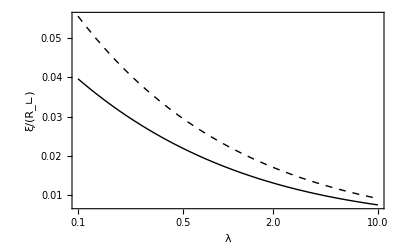

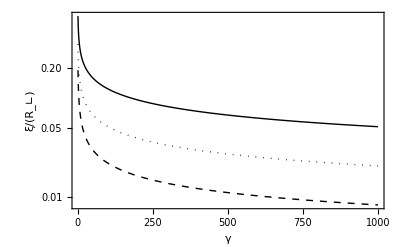

```mathematica
fig1=LogLinearPlot[{(π^(1/4)*√(z0/(8*800*2)))/.FindRoot[{eqs1,eqs2}/.γ->50/.λ->c/.L->1,{r0,0.001},{z0,0.001}],(π^(1/4)*√(z0/(8*800*2)))/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->1,{r0,0.001},{z0,0.001}]},{c,0.1,10},RotateLabel->False,FrameLabel->{λ,ξ/Subscript[R,"∟"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Directive[Black,Dashed]}]
fig2=LogPlot[{(π^(1/4)*√(z0/(8*c*2)))/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->1,{r0,0.001},{z0,0.001}],(π^(1/4)*√(z0/(8*c*2)))/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->1,{r0,0.001},{z0,0.001}],(π^(1/4)*√(z0/(8*c*2)))/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->1,{r0,0.001},{z0,0.001}]},{c,1,1000},RotateLabel->False,FrameLabel->{γ,ξ/Subscript[R,"∟"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Directive[Black,Dotted],Directive[Black,Dashed]}]
```

1.0084

1.

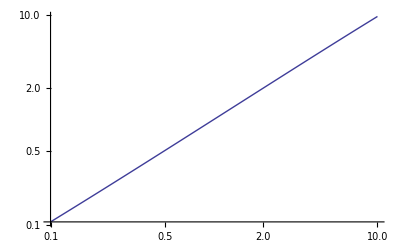

```mathematica
(Evaluate[r0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->1/.L->1,{r0,0.001},{z0,0.001}]]*√2)/Evaluate[z0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->1/.L->1,{r0,0.001},{z0,0.001}]]
Evaluate[r0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->1/.L->0,{r0,0.001},{z0,0.001}]]/Evaluate[z0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->1/.L->0,{r0,0.001},{z0,0.001}]]
f99=LogLogPlot[(Evaluate[r0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->1,{r0,0.001},{z0,0.001}]]*√2)/Evaluate[z0/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->1,{r0,0.001},{z0,0.001}]],{c,0.1,10}]
```

## Energy

```mathematica
Ef[L_,γ_,λ_,R_,Z_]:=((L+1)/2)*(1/R^2+R^2)+1/4*(1/Z^2+λ^2*Z^2)+(γ*Factorial[2 L])/(2^(2 L) √(2 π)*Factorial[L]^2*R^2*Z)
```

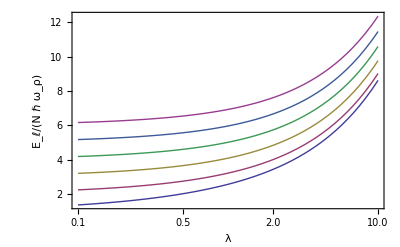

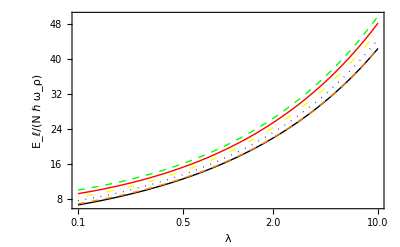

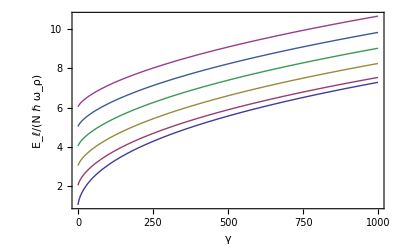

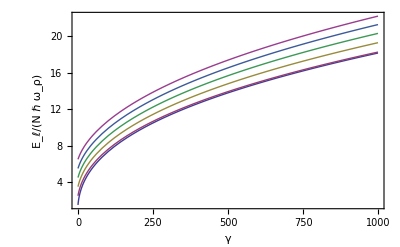

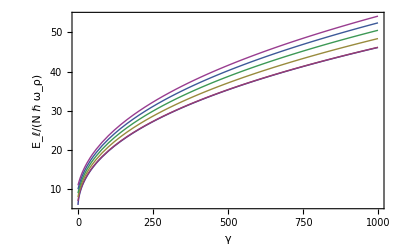

```mathematica
fig3=LogLinearPlot[{Ef[0,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->0,{r0,0.001},{z0,0.001}],Ef[1,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->1,{r0,0.001},{z0,0.001}],Ef[2,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->2,{r0,0.001},{z0,0.001}],Ef[3,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->3,{r0,0.001},{z0,0.001}],Ef[4,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->4,{r0,0.001},{z0,0.001}],Ef[5,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->5,{r0,0.001},{z0,0.001}]},{c,0.1,10},RotateLabel->False,FrameLabel->{λ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->All,Frame->True,Axes->False,PlotLegend->{ℓ==0,ℓ==1,ℓ==2,ℓ==3,ℓ==4,ℓ==5},LegendPosition->{-0.64,0},LegendSize->{0.3,0.5},LegendShadow->{0,0}]
fig4=LogLinearPlot[{Ef[0,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->0,{r0,0.001},{z0,0.001}],Ef[1,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->1,{r0,0.001},{z0,0.001}],Ef[2,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->2,{r0,0.001},{z0,0.001}],Ef[3,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->3,{r0,0.001},{z0,0.001}],Ef[4,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->4,{r0,0.001},{z0,0.001}],Ef[5,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->5,{r0,0.001},{z0,0.001}]},{c,0.1,10},RotateLabel->False,FrameLabel->{λ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotLegend->{ℓ==0,ℓ==1,ℓ==2,ℓ==3,ℓ==4,ℓ==5},LegendPosition->{-0.60,-0.10},LegendSize->{0.3,0.5},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed]}]
fig5=Plot[{Ef[0,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->0,{r0,0.001},{z0,0.001}],Ef[1,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->1,{r0,0.001},{z0,0.001}],Ef[2,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->2,{r0,0.001},{z0,0.001}],Ef[3,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->3,{r0,0.001},{z0,0.001}],Ef[4,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->4,{r0,0.001},{z0,0.001}],Ef[5,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->5,{r0,0.001},{z0,0.001}]},{c,0,1000},RotateLabel->False,FrameLabel->{γ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->All,Frame->True,Axes->False,PlotLegend->{ℓ==0,ℓ==1,ℓ==2,ℓ==3,ℓ==4,ℓ==5},LegendPosition->{0.5,-0.4},LegendSize->{0.3,0.5},LegendShadow->{0,0}]
fig6=Plot[{Ef[0,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->0,{r0,0.001},{z0,0.001}],Ef[1,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->1,{r0,0.001},{z0,0.001}],Ef[2,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->2,{r0,0.001},{z0,0.001}],Ef[3,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->3,{r0,0.001},{z0,0.001}],Ef[4,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->4,{r0,0.001},{z0,0.001}],Ef[5,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->5,{r0,0.001},{z0,0.001}]},{c,0,1000},RotateLabel->False,FrameLabel->{γ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->All,Frame->True,Axes->False,PlotLegend->{ℓ==0,ℓ==1,ℓ==2,ℓ==3,ℓ==4,ℓ==5},LegendPosition->{0.5,-0.4},LegendSize->{0.3,0.5},LegendShadow->{0,0}]
fig7=Plot[{Ef[0,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->0,{r0,0.001},{z0,0.001}],Ef[1,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->1,{r0,0.001},{z0,0.001}],Ef[2,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->2,{r0,0.001},{z0,0.001}],Ef[3,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->3,{r0,0.001},{z0,0.001}],Ef[4,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->4,{r0,0.001},{z0,0.001}],Ef[5,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->5,{r0,0.001},{z0,0.001}]},{c,0,1000},RotateLabel->False,FrameLabel->{γ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->All,Frame->True,Axes->False,PlotLegend->{ℓ==0,ℓ==1,ℓ==2,ℓ==3,ℓ==4,ℓ==5},LegendPosition->{0.5,-0.4},LegendSize->{0.3,0.5},LegendShadow->{0,0}]
```

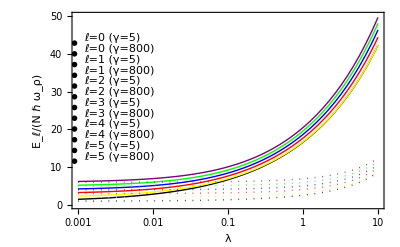

```mathematica
fig8=LogLinearPlot[{Ef[0,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->0,{r0,0.001},{z0,0.001}],Ef[0,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->0,{r0,0.001},{z0,0.001}],Ef[1,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->1,{r0,0.001},{z0,0.001}],Ef[1,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->1,{r0,0.001},{z0,0.001}],Ef[2,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->2,{r0,0.001},{z0,0.001}],Ef[2,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->2,{r0,0.001},{z0,0.001}],Ef[3,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->3,{r0,0.001},{z0,0.001}],Ef[3,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->3,{r0,0.001},{z0,0.001}],Ef[4,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->4,{r0,0.001},{z0,0.001}],Ef[4,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->4,{r0,0.001},{z0,0.001}],Ef[5,5,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->5/.λ->c/.L->5,{r0,0.001},{z0,0.001}],Ef[5,800,c,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->800/.λ->c/.L->5,{r0,0.001},{z0,0.001}]},{c,0.001,10},RotateLabel->False,FrameLabel->{λ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->{0,50},Frame->True,Axes->False,PlotLegend->{"ℓ=0 (γ=5)","ℓ=0 (γ=800)","ℓ=1 (γ=5)","ℓ=1 (γ=800)","ℓ=2 (γ=5)","ℓ=2 (γ=800)","ℓ=3 (γ=5)","ℓ=3 (γ=800)","ℓ=4 (γ=5)","ℓ=4 (γ=800)","ℓ=5 (γ=5)","ℓ=5 (γ=800)"},LegendPosition->{-0.67,-0.27},LegendShadow->{0,0},LegendSize->{0.4,0.8},PlotStyle->{Directive[Black,Dotted],Black,Directive[Yellow,Dotted],Yellow,Directive[Red,Dotted],Red,Directive[Blue,Dotted],Blue,Directive[Green,Dotted],Green,Directive[Purple,Dotted],Purple},LegendTextSpace->5]
```

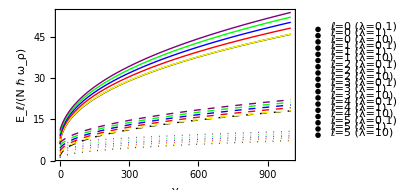

```mathematica
fig9=Plot[{Ef[0,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->0,{r0,0.001},{z0,0.001}],Ef[0,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->0,{r0,0.001},{z0,0.001}],Ef[0,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->0,{r0,0.001},{z0,0.001}],Ef[1,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->1,{r0,0.001},{z0,0.001}],Ef[1,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->1,{r0,0.001},{z0,0.001}],Ef[1,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->1,{r0,0.001},{z0,0.001}],Ef[2,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->2,{r0,0.001},{z0,0.001}],Ef[2,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->2,{r0,0.001},{z0,0.001}],Ef[2,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->2,{r0,0.001},{z0,0.001}],Ef[3,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->3,{r0,0.001},{z0,0.001}],Ef[3,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->3,{r0,0.001},{z0,0.001}],Ef[3,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->3,{r0,0.001},{z0,0.001}],Ef[4,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->4,{r0,0.001},{z0,0.001}],Ef[4,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->4,{r0,0.001},{z0,0.001}],Ef[4,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->4,{r0,0.001},{z0,0.001}],Ef[5,c,0.1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->0.1/.L->5,{r0,0.001},{z0,0.001}],Ef[5,c,1,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->1/.L->5,{r0,0.001},{z0,0.001}],Ef[5,c,10,r0,z0]/.FindRoot[{eqs1,eqs2}/.γ->c/.λ->10/.L->5,{r0,0.001},{z0,0.001}]},{c,0,1000},RotateLabel->False,FrameLabel->{γ,Subscript[Ε,ℓ]/(Ν*ℏ*Subscript[ω,ρ])},PlotRange->All,Frame->True,Axes->False,PlotLegend->{"ℓ=0 (λ=0.1)","ℓ=0 (λ=1)","ℓ=0 (λ=10)","ℓ=1 (λ=0.1)","ℓ=1 (λ=1)","ℓ=1 (λ=10)","ℓ=2 (λ=0.1)","ℓ=2 (λ=1)","ℓ=2 (λ=10)","ℓ=3 (λ=0.1)","ℓ=3 (λ=1)","ℓ=3 (λ=10)","ℓ=4 (λ=0.1)","ℓ=4 (λ=1)","ℓ=4 (λ=10)","ℓ=5 (λ=0.1)","ℓ=5 (λ=1)","ℓ=5 (λ=10)"},LegendPosition->{1,-0.35},LegendShadow->{0,0},PlotStyle->{Directive[Black,Dotted],Directive[Black,Dashed],Black,Directive[Yellow,Dotted],Directive[Yellow,Dashed],Yellow,Directive[Red,Dotted],Directive[Red,Dashed],Red,Directive[Blue,Dotted],Directive[Blue,Dashed],Blue,Directive[Green,Dotted],Directive[Green,Dashed],Green,Directive[Purple,Dotted],Directive[Purple,Dashed],Purple},LegendTextSpace->5,LegendSize->{0.6,0.9}]
```

## Expansion

```mathematica
exp1=D[R[t],{t,2}]==1/R[t]^3+(γ*(L+1)*Gamma[2*L+1])/(2^(2*L-1)*√(2*π)*Gamma[L+2]^2*R[t]^3*Z[t])
exp2=D[Z[t],{t,2}]==1/Z[t]^3+(γ*Gamma[2*L+1])/(2^(2*L-1)*√(2*π)*Gamma[L+1]^2*R[t]^2*Z[t]^2)
```

R''[t]==1/R[t]^3+(2^(1/2-2 L) (1+L) γ Gamma[1+2 L])/(√π Gamma[2+L]^2 R[t]^3 Z[t])

Z''[t]==1/Z[t]^3+(2^(1/2-2 L) γ Gamma[1+2 L])/(√π Gamma[1+L]^2 R[t]^2 Z[t]^2)

```mathematica
A[L_,t_]:=(R[t]*√(L+1))/Z[t]
A0[t_]:=R[t]/Z[t]
Al[t_]:=(√(1+t^2))/(√(λ^-1+λ t^2))
```

### λ = 0.1 e γ = 800

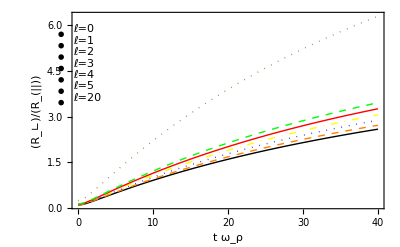

{2.30789}

{2.37656}

{2.52077}

{2.67211}

{2.82298}

{2.97118}

{4.78815}

{0.343149}

{0.336805}

{0.33688}

{0.335738}

{0.333627}

{0.330978}

{0.294063}

```mathematica
λ=0.1;
γ=800;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->0/.FindRoot[{eqs1,eqs2}/.L->0,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->1/.FindRoot[{eqs1,eqs2}/.L->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->2/.FindRoot[{eqs1,eqs2}/.L->2,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->3/.FindRoot[{eqs1,eqs2}/.L->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s4=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->4/.FindRoot[{eqs1,eqs2}/.L->4,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s5=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->5/.FindRoot[{eqs1,eqs2}/.L->5,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s20=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->20/.FindRoot[{eqs1,eqs2}/.L->20,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
fig10=Plot[{A0[t]/.s0,A[1,t]/.s1,A[2,t]/.s2,A[3,t]/.s3,A[4,t]/.s4,A[5,t]/.s5,A[20,t]/.s20},{t,0,40},PlotRange->All,RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"∟"]/Subscript[R,"||"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
((Evaluate[R[t]/.s0]/.t->1000)-(Evaluate[R[t]/.s0]/.t->700))/300
((Evaluate[R[t]*√2/.s1]/.t->1000)-(Evaluate[R[t]*√2/.s1]/.t->700))/300
((Evaluate[R[t]*√3/.s2]/.t->1000)-(Evaluate[R[t]*√3/.s2]/.t->700))/300
((Evaluate[R[t]*√4/.s3]/.t->1000)-(Evaluate[R[t]*√4/.s3]/.t->700))/300
((Evaluate[R[t]*√5/.s4]/.t->1000)-(Evaluate[R[t]*√5/.s4]/.t->700))/300
((Evaluate[R[t]*√6/.s5]/.t->1000)-(Evaluate[R[t]*√6/.s5]/.t->700))/300
((Evaluate[R[t]*√21/.s20]/.t->1000)-(Evaluate[R[t]*√21/.s20]/.t->700))/300
((Evaluate[Z[t]/.s0]/.t->1000)-(Evaluate[Z[t]/.s0]/.t->700))/300
((Evaluate[Z[t]/.s1]/.t->1000)-(Evaluate[Z[t]/.s1]/.t->700))/300
((Evaluate[Z[t]/.s2]/.t->1000)-(Evaluate[Z[t]/.s2]/.t->700))/300
((Evaluate[Z[t]/.s3]/.t->1000)-(Evaluate[Z[t]/.s3]/.t->700))/300
((Evaluate[Z[t]/.s4]/.t->1000)-(Evaluate[Z[t]/.s4]/.t->700))/300
((Evaluate[Z[t]/.s5]/.t->1000)-(Evaluate[Z[t]/.s5]/.t->700))/300
((Evaluate[Z[t]/.s20]/.t->1000)-(Evaluate[Z[t]/.s20]/.t->700))/300

ClearAll[λ,γ,s0,s1,s2,s3,s4,s5,s20]
```

### λ = 1 e γ = 800

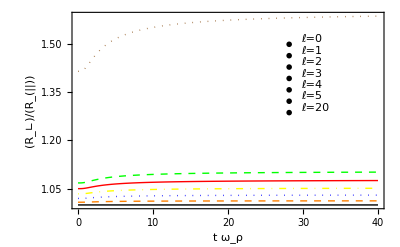

{2.979}

{3.00688}

{3.11739}

{3.23098}

{3.3432}

{3.45401}

{4.98092}

{2.979}

{2.96812}

{3.02279}

{3.06804}

{3.1021}

{3.12706}

{3.1146}

```mathematica
λ=1;
γ=800;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->0/.FindRoot[{eqs1,eqs2}/.L->0,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->1/.FindRoot[{eqs1,eqs2}/.L->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->2/.FindRoot[{eqs1,eqs2}/.L->2,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->3/.FindRoot[{eqs1,eqs2}/.L->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s4=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->4/.FindRoot[{eqs1,eqs2}/.L->4,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s5=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->5/.FindRoot[{eqs1,eqs2}/.L->5,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s20=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->20/.FindRoot[{eqs1,eqs2}/.L->20,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
fig11=Plot[{A0[t]/.s0,A[1,t]/.s1,A[2,t]/.s2,A[3,t]/.s3,A[4,t]/.s4,A[5,t]/.s5,A[20,t]/.s20},{t,0,40},PlotRange->All,RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"∟"]/Subscript[R,"||"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{0.4,0},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
((Evaluate[R[t]/.s0]/.t->1000)-(Evaluate[R[t]/.s0]/.t->700))/300
((Evaluate[R[t]*√2/.s1]/.t->1000)-(Evaluate[R[t]*√2/.s1]/.t->700))/300
((Evaluate[R[t]*√3/.s2]/.t->1000)-(Evaluate[R[t]*√3/.s2]/.t->700))/300
((Evaluate[R[t]*√4/.s3]/.t->1000)-(Evaluate[R[t]*√4/.s3]/.t->700))/300
((Evaluate[R[t]*√5/.s4]/.t->1000)-(Evaluate[R[t]*√5/.s4]/.t->700))/300
((Evaluate[R[t]*√6/.s5]/.t->1000)-(Evaluate[R[t]*√6/.s5]/.t->700))/300
((Evaluate[R[t]*√21/.s20]/.t->1000)-(Evaluate[R[t]*√21/.s20]/.t->700))/300
((Evaluate[Z[t]/.s0]/.t->1000)-(Evaluate[Z[t]/.s0]/.t->700))/300
((Evaluate[Z[t]/.s1]/.t->1000)-(Evaluate[Z[t]/.s1]/.t->700))/300
((Evaluate[Z[t]/.s2]/.t->1000)-(Evaluate[Z[t]/.s2]/.t->700))/300
((Evaluate[Z[t]/.s3]/.t->1000)-(Evaluate[Z[t]/.s3]/.t->700))/300
((Evaluate[Z[t]/.s4]/.t->1000)-(Evaluate[Z[t]/.s4]/.t->700))/300
((Evaluate[Z[t]/.s5]/.t->1000)-(Evaluate[Z[t]/.s5]/.t->700))/300
((Evaluate[Z[t]/.s20]/.t->1000)-(Evaluate[Z[t]/.s20]/.t->700))/300
ClearAll[λ,γ,s0,s1,s2,s3,s4,s5,s20]
```

### λ = 10 e γ = 800

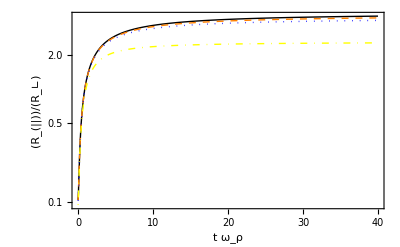

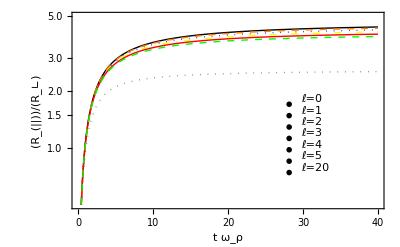

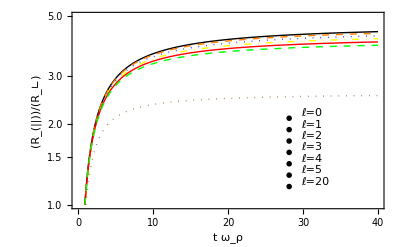

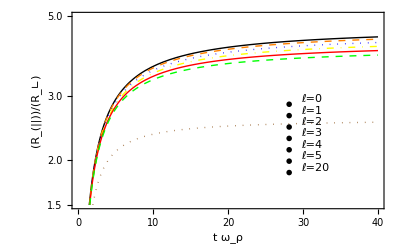

{1.68352}

{1.71126}

{1.79101}

{1.87678}

{1.96543}

{2.05645}

{3.53137}

{7.91374}

{7.90882}

{8.08053}

{8.23557}

{8.36748}

{8.48004}

{9.19049}

```mathematica
λ=10;
γ=800;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->0/.FindRoot[{eqs1,eqs2}/.L->0,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->1/.FindRoot[{eqs1,eqs2}/.L->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->2/.FindRoot[{eqs1,eqs2}/.L->2,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->3/.FindRoot[{eqs1,eqs2}/.L->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s4=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->4/.FindRoot[{eqs1,eqs2}/.L->4,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s5=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->5/.FindRoot[{eqs1,eqs2}/.L->5,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s20=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.L->20/.FindRoot[{eqs1,eqs2}/.L->20,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
fig12=LogPlot[{A0[t]^-1/.s0,A[2,t]^-1/.s2,A[4,t]^-1/.s4,A[20,t]^-1/.s20},{t,0,40},PlotRange->All,RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"||"]/Subscript[R,"∟"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=2","ℓ=4","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{0.4,-0.3},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
fig12a=LogPlot[{A0[t]^-1/.s0,A[1,t]^-1/.s1,A[2,t]^-1/.s2,A[3,t]^-1/.s3,A[4,t]^-1/.s4,A[5,t]^-1/.s5,A[20,t]^-1/.s20},{t,0,40},PlotRange->{{0,40},{0.5,5}},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"||"]/Subscript[R,"∟"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{0.4,-0.3},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
fig12b=LogPlot[{A0[t]^-1/.s0,A[1,t]^-1/.s1,A[2,t]^-1/.s2,A[3,t]^-1/.s3,A[4,t]^-1/.s4,A[5,t]^-1/.s5,A[20,t]^-1/.s20},{t,0,40},PlotRange->{{0,40},{1,5}},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"||"]/Subscript[R,"∟"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{0.4,-0.37},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
fig12c=LogPlot[{A0[t]^-1/.s0,A[1,t]^-1/.s1,A[2,t]^-1/.s2,A[3,t]^-1/.s3,A[4,t]^-1/.s4,A[5,t]^-1/.s5,A[20,t]^-1/.s20},{t,0,40},PlotRange->{{0,40},{1.5,5}},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,Subscript[R,"||"]/Subscript[R,"∟"]},LabelStyle->{Medium},Axes->False,Frame->True,PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.4,0.5},LegendPosition->{0.4,-0.3},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
((Evaluate[R[t]/.s0]/.t->1000)-(Evaluate[R[t]/.s0]/.t->700))/300
((Evaluate[R[t]*√2/.s1]/.t->1000)-(Evaluate[R[t]*√2/.s1]/.t->700))/300
((Evaluate[R[t]*√3/.s2]/.t->1000)-(Evaluate[R[t]*√3/.s2]/.t->700))/300
((Evaluate[R[t]*√4/.s3]/.t->1000)-(Evaluate[R[t]*√4/.s3]/.t->700))/300
((Evaluate[R[t]*√5/.s4]/.t->1000)-(Evaluate[R[t]*√5/.s4]/.t->700))/300
((Evaluate[R[t]*√6/.s5]/.t->1000)-(Evaluate[R[t]*√6/.s5]/.t->700))/300
((Evaluate[R[t]*√21/.s20]/.t->1000)-(Evaluate[R[t]*√21/.s20]/.t->700))/300
((Evaluate[Z[t]/.s0]/.t->1000)-(Evaluate[Z[t]/.s0]/.t->700))/300
((Evaluate[Z[t]/.s1]/.t->1000)-(Evaluate[Z[t]/.s1]/.t->700))/300
((Evaluate[Z[t]/.s2]/.t->1000)-(Evaluate[Z[t]/.s2]/.t->700))/300
((Evaluate[Z[t]/.s3]/.t->1000)-(Evaluate[Z[t]/.s3]/.t->700))/300
((Evaluate[Z[t]/.s4]/.t->1000)-(Evaluate[Z[t]/.s4]/.t->700))/300
((Evaluate[Z[t]/.s5]/.t->1000)-(Evaluate[Z[t]/.s5]/.t->700))/300
((Evaluate[Z[t]/.s20]/.t->1000)-(Evaluate[Z[t]/.s20]/.t->700))/300

ClearAll[λ,γ,s0,s1,s2,s3,s4,s5,s20,d]
```

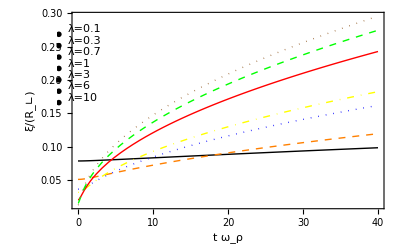

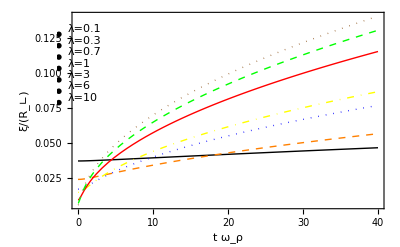

{0.0373921}

{0.0468012}

{{0.0233964}}

```mathematica
γ=800;
L=1;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.1/.FindRoot[{eqs1,eqs2}/.λ->0.1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.3/.FindRoot[{eqs1,eqs2}/.λ->0.3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.7/.FindRoot[{eqs1,eqs2}/.λ->0.7,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->1/.FindRoot[{eqs1,eqs2}/.λ->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s4=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->3/.FindRoot[{eqs1,eqs2}/.λ->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s5=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->6/.FindRoot[{eqs1,eqs2}/.λ->6,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s20=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->10/.FindRoot[{eqs1,eqs2}/.λ->10,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
fig13=Plot[{(π^(1/4)*√(Z[t]/(8*γ)))/.s0,(π^(1/4)*√(Z[t]/(8*γ)))/.s1,(π^(1/4)*√(Z[t]/(8*γ)))/.s2,(π^(1/4)*√(Z[t]/(8*γ)))/.s3,(π^(1/4)*√(Z[t]/(8*γ)))/.s4,(π^(1/4)*√(Z[t]/(8*γ)))/.s5,(π^(1/4)*√(Z[t]/(8*γ)))/.s20},{t,0,40},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,ξ/Subscript[R,"∟"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotLegend->{"λ=0.1","λ=0.3","λ=0.7","λ=1","λ=3","λ=6","λ=10"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]}]
ClearAll[γ,L,s0,s1,s2,s3,s4,s5,s20]
γ=800;
L=1;
s0=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.1/.FindRoot[{eqs1,eqs2}/.λ->0.1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s1=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.3/.FindRoot[{eqs1,eqs2}/.λ->0.3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s2=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->0.7/.FindRoot[{eqs1,eqs2}/.λ->0.7,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s3=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->1/.FindRoot[{eqs1,eqs2}/.λ->1,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s4=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->3/.FindRoot[{eqs1,eqs2}/.λ->3,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s5=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->6/.FindRoot[{eqs1,eqs2}/.λ->6,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
s20=NDSolve[{exp1,exp2,R[0]==r0,Z[0]==z0,R'[0]==0,Z'[0]==0}/.λ->10/.FindRoot[{eqs1,eqs2}/.λ->10,{r0,0.01},{z0,0.01}],{R[t],Z[t]},{t,0,1000}];
fig13b=Plot[{(1/2 √(Z[t]/(5*γ)))/.s0,(1/2 √(Z[t]/(5*γ)))/.s1,(1/2 √(Z[t]/(5*γ)))/.s2,(1/2 √(Z[t]/(5*γ)))/.s3,(1/2 √(Z[t]/(5*γ)))/.s4,(1/2 √(Z[t]/(5*γ)))/.s5,(1/2 √(Z[t]/(5*γ)))/.s20},{t,0,40},RotateLabel->False,FrameLabel->{Subscript[ω,ρ]*t,ξ/Subscript[R,"∟"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Directive[Black],Directive[Orange,Dashed],Directive[Blue,Dotted],Directive[Yellow,DotDashed],Directive[Red,Thick],Directive[Green,Thick,Dashed],Directive[Brown,Thick,Dotted]},PlotLegend->{"λ=0.1","λ=0.3","λ=0.7","λ=1","λ=3","λ=6","λ=10"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0}]
(1/2 √(Z[t]/(5*γ)))/.s0/.t->0
(1/2 √(Z[t]/(5*γ)))/.s0/.t->40
((1/2 √(Z[t]/(5*γ)))/.s0/.t->40-(1/2 √(Z[t]/(5*γ)))/.s0/.t->0)/2
ClearAll[γ,L,s0,s1,s2,s3,s4,s5,s20]
```

## Velocity

### λ = 0.1

```mathematica
λ=0.1;
L=0;
γmax=5000;
dγ=50;
f0=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g0=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=1;
f1=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g1=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=2;
f2=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g2=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=3;
f3=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g3=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=4;
f4=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g4=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=5;
f5=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g5=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=20;
f20=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g20=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L,λ,γmax]
```

```mathematica
Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

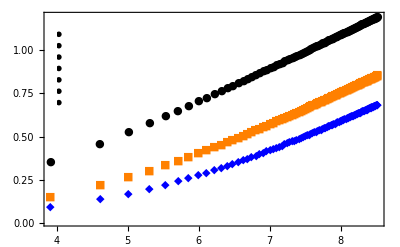

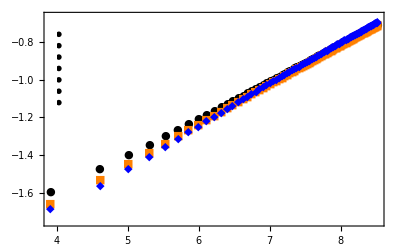

```mathematica
fig14=ListLogLogPlot[{f0,f1,f2,f3,f4,f5,f20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"∟"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
fig15=ListLogLogPlot[{g0,g1,g2,g3,g4,g5,g20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"||"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
```

```mathematica
ClearAll[Aρ,Az]
Aρ[L_]:=((Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+2]))*(1/(2^(2*L-1)*√(2*π))))^-1
Az[L_]:=((Gamma[2*L+1]/(Gamma[L+1]*Gamma[L+1]))*(1/(2^(2*L-1)*√(2*π))))^-1
```

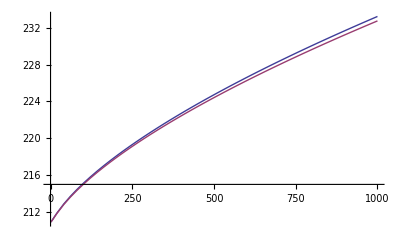

```mathematica
ClearAll[L,λ,γ]
L=20;
λ=0.1;
Plot[{Aρ[L]*((Evaluate[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,10000}]]/.t->10000)/2000-(Evaluate[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,10000}]]/.t->8000)/2000)^2+Az[L]*((Evaluate[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,10000}]]/.t->10000)/2000-(Evaluate[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,10000}]]/.t->8000)/2000)^2,Aρ[L]*Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]]^-2+Az[L]*Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]]^-2+γ*Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]]^-2*Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]]^-1},{γ,0,1000}]
```

### λ = 1

```mathematica
ClearAll[f0,f1,f2,f3,f4,f5,f20,g0,g1,g2,g3,g4,g5,g20]
λ=1;
L=0;
γmax=5000;
dγ=50;
f0=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g0=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=1;
f1=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g1=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=2;
f2=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g2=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=3;
f3=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g3=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=4;
f4=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g4=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=5;
f5=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g5=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=20;
f20=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g20=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L,λ]
ClearAll[λ,L,γmax,dγ]
```

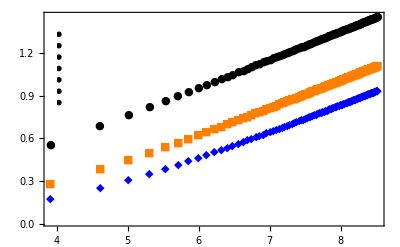

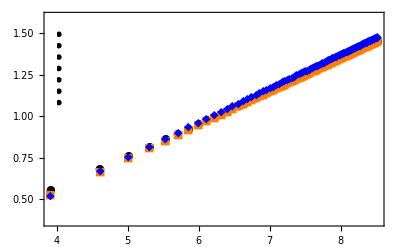

```mathematica
fig16=ListLogLogPlot[{f0,f1,f2,f3,f4,f5,f20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"∟"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
fig17=ListLogLogPlot[{g0,g1,g2,g3,g4,g5,g20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"||"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
```

```mathematica
(Log[Extract[f0,{10001,2}]]-Log[Extract[f0,{501,2}]])/(Log[Extract[f0,{10001,1}]]-Log[Extract[f0,{501,1}]])
(Log[Extract[f1,{10001,2}]]-Log[Extract[f1,{501,2}]])/(Log[Extract[f1,{10001,1}]]-Log[Extract[f1,{501,1}]])
(Log[Extract[f2,{10001,2}]]-Log[Extract[f2,{501,2}]])/(Log[Extract[f2,{10001,1}]]-Log[Extract[f2,{501,1}]])
(Log[Extract[f3,{10001,2}]]-Log[Extract[f3,{501,2}]])/(Log[Extract[f3,{10001,1}]]-Log[Extract[f3,{501,1}]])
(Log[Extract[f4,{10001,2}]]-Log[Extract[f4,{501,2}]])/(Log[Extract[f4,{10001,1}]]-Log[Extract[f4,{501,1}]])
(Log[Extract[f5,{10001,2}]]-Log[Extract[f5,{501,2}]])/(Log[Extract[f5,{10001,1}]]-Log[Extract[f5,{501,1}]])
(Log[Extract[f20,{10001,2}]]-Log[Extract[f20,{501,2}]])/(Log[Extract[f20,{10001,1}]]-Log[Extract[f20,{501,1}]])
```

(-Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.3238},{100,1.46781},{150,1.56873},{200,1.64808},{250,1.71416},{300,1.77115},{350,1.82147},{400,1.86667},{450,1.9078},{500,1.9456},{550,1.98063},{600,2.01331},{650,2.04396},{700,2.07286},{750,2.10021},{800,2.12619},{850,2.15094},{900,2.17459},{950,2.19725},{1000,2.219},{1050,2.23992},{1100,2.26008},{1150,2.27954},{1200,2.29835},{1250,2.31655},{1300,2.3342},{1350,2.35133},{1400,2.36797},{1450,2.38415},{1500,2.3999},{1550,2.41524},{1600,2.4302},{1650,2.4448},{1700,2.45905},{1750,2.47298},{1800,2.48661},{1850,2.49993},{1900,2.51298},{1950,2.52576},{2000,2.53829},{2050,2.55057},{2100,2.56262},{2150,2.57444},{2200,2.58605},{2250,2.59746},{2300,2.60866},{2350,2.61968},{2400,2.63051},{2450,2.64117},{2500,2.65165},{2550,2.66197},{2600,2.67214},{2650,2.68215},{2700,2.69201},{2750,2.70173},{2800,2.71131},{2850,2.72076},{2900,2.73008},{2950,2.73927},{3000,2.74834},{3050,2.75729},{3100,2.76612},{3150,2.77485},{3200,2.78346},{3250,2.79197},{3300,2.80037},{3350,2.80868},{3400,2.81689},{3450,2.825},{3500,2.83302},{3550,2.84095},{3600,2.8488},{3650,2.85655},{3700,2.86423},{3750,2.87182},{3800,2.87933},{3850,2.88676},{3900,2.89412},{3950,2.90141},{4000,2.90862},{4050,2.91576},{4100,2.92283},{4150,2.92983},{4200,2.93677},{4250,2.94364},{4300,2.95044},{4350,2.95719},{4400,2.96387},{4450,2.97049},{4500,2.97706},{4550,2.98357},{4600,2.99002},{4650,2.99641},{4700,3.00275},{4750,3.00904},{4800,3.01528},{4850,3.02146},{4900,3.0276},{4950,3.03368},{5000,3.03972}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.3238},{100,1.46781},{150,1.56873},{200,1.64808},{250,1.71416},{300,1.77115},{350,1.82147},{400,1.86667},{450,1.9078},{500,1.9456},{550,1.98063},{600,2.01331},{650,2.04396},{700,2.07286},{750,2.10021},{800,2.12619},{850,2.15094},{900,2.17459},{950,2.19725},{1000,2.219},{1050,2.23992},{1100,2.26008},{1150,2.27954},{1200,2.29835},{1250,2.31655},{1300,2.3342},{1350,2.35133},{1400,2.36797},{1450,2.38415},{1500,2.3999},{1550,2.41524},{1600,2.4302},{1650,2.4448},{1700,2.45905},{1750,2.47298},{1800,2.48661},{1850,2.49993},{1900,2.51298},{1950,2.52576},{2000,2.53829},{2050,2.55057},{2100,2.56262},{2150,2.57444},{2200,2.58605},{2250,2.59746},{2300,2.60866},{2350,2.61968},{2400,2.63051},{2450,2.64117},{2500,2.65165},{2550,2.66197},{2600,2.67214},{2650,2.68215},{2700,2.69201},{2750,2.70173},{2800,2.71131},{2850,2.72076},{2900,2.73008},{2950,2.73927},{3000,2.74834},{3050,2.75729},{3100,2.76612},{3150,2.77485},{3200,2.78346},{3250,2.79197},{3300,2.80037},{3350,2.80868},{3400,2.81689},{3450,2.825},{3500,2.83302},{3550,2.84095},{3600,2.8488},{3650,2.85655},{3700,2.86423},{3750,2.87182},{3800,2.87933},{3850,2.88676},{3900,2.89412},{3950,2.90141},{4000,2.90862},{4050,2.91576},{4100,2.92283},{4150,2.92983},{4200,2.93677},{4250,2.94364},{4300,2.95044},{4350,2.95719},{4400,2.96387},{4450,2.97049},{4500,2.97706},{4550,2.98357},{4600,2.99002},{4650,2.99641},{4700,3.00275},{4750,3.00904},{4800,3.01528},{4850,3.02146},{4900,3.0276},{4950,3.03368},{5000,3.03972}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.3238},{100,1.46781},{150,1.56873},{200,1.64808},{250,1.71416},{300,1.77115},{350,1.82147},{400,1.86667},{450,1.9078},{500,1.9456},{550,1.98063},{600,2.01331},{650,2.04396},{700,2.07286},{750,2.10021},{800,2.12619},{850,2.15094},{900,2.17459},{950,2.19725},{1000,2.219},{1050,2.23992},{1100,2.26008},{1150,2.27954},{1200,2.29835},{1250,2.31655},{1300,2.3342},{1350,2.35133},{1400,2.36797},{1450,2.38415},{1500,2.3999},{1550,2.41524},{1600,2.4302},{1650,2.4448},{1700,2.45905},{1750,2.47298},{1800,2.48661},{1850,2.49993},{1900,2.51298},{1950,2.52576},{2000,2.53829},{2050,2.55057},{2100,2.56262},{2150,2.57444},{2200,2.58605},{2250,2.59746},{2300,2.60866},{2350,2.61968},{2400,2.63051},{2450,2.64117},{2500,2.65165},{2550,2.66197},{2600,2.67214},{2650,2.68215},{2700,2.69201},{2750,2.70173},{2800,2.71131},{2850,2.72076},{2900,2.73008},{2950,2.73927},{3000,2.74834},{3050,2.75729},{3100,2.76612},{3150,2.77485},{3200,2.78346},{3250,2.79197},{3300,2.80037},{3350,2.80868},{3400,2.81689},{3450,2.825},{3500,2.83302},{3550,2.84095},{3600,2.8488},{3650,2.85655},{3700,2.86423},{3750,2.87182},{3800,2.87933},{3850,2.88676},{3900,2.89412},{3950,2.90141},{4000,2.90862},{4050,2.91576},{4100,2.92283},{4150,2.92983},{4200,2.93677},{4250,2.94364},{4300,2.95044},{4350,2.95719},{4400,2.96387},{4450,2.97049},{4500,2.97706},{4550,2.98357},{4600,2.99002},{4650,2.99641},{4700,3.00275},{4750,3.00904},{4800,3.01528},{4850,3.02146},{4900,3.0276},{4950,3.03368},{5000,3.03972}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.3238},{100,1.46781},{150,1.56873},{200,1.64808},{250,1.71416},{300,1.77115},{350,1.82147},{400,1.86667},{450,1.9078},{500,1.9456},{550,1.98063},{600,2.01331},{650,2.04396},{700,2.07286},{750,2.10021},{800,2.12619},{850,2.15094},{900,2.17459},{950,2.19725},{1000,2.219},{1050,2.23992},{1100,2.26008},{1150,2.27954},{1200,2.29835},{1250,2.31655},{1300,2.3342},{1350,2.35133},{1400,2.36797},{1450,2.38415},{1500,2.3999},{1550,2.41524},{1600,2.4302},{1650,2.4448},{1700,2.45905},{1750,2.47298},{1800,2.48661},{1850,2.49993},{1900,2.51298},{1950,2.52576},{2000,2.53829},{2050,2.55057},{2100,2.56262},{2150,2.57444},{2200,2.58605},{2250,2.59746},{2300,2.60866},{2350,2.61968},{2400,2.63051},{2450,2.64117},{2500,2.65165},{2550,2.66197},{2600,2.67214},{2650,2.68215},{2700,2.69201},{2750,2.70173},{2800,2.71131},{2850,2.72076},{2900,2.73008},{2950,2.73927},{3000,2.74834},{3050,2.75729},{3100,2.76612},{3150,2.77485},{3200,2.78346},{3250,2.79197},{3300,2.80037},{3350,2.80868},{3400,2.81689},{3450,2.825},{3500,2.83302},{3550,2.84095},{3600,2.8488},{3650,2.85655},{3700,2.86423},{3750,2.87182},{3800,2.87933},{3850,2.88676},{3900,2.89412},{3950,2.90141},{4000,2.90862},{4050,2.91576},{4100,2.92283},{4150,2.92983},{4200,2.93677},{4250,2.94364},{4300,2.95044},{4350,2.95719},{4400,2.96387},{4450,2.97049},{4500,2.97706},{4550,2.98357},{4600,2.99002},{4650,2.99641},{4700,3.00275},{4750,3.00904},{4800,3.01528},{4850,3.02146},{4900,3.0276},{4950,3.03368},{5000,3.03972}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.19165},{100,1.29156},{150,1.36511},{200,1.42449},{250,1.4748},{300,1.51871},{350,1.55783},{400,1.59322},{450,1.6256},{500,1.65549},{550,1.68331},{600,1.70934},{650,1.73383},{700,1.75697},{750,1.77893},{800,1.79982},{850,1.81977},{900,1.83885},{950,1.85716},{1000,1.87476},{1050,1.89171},{1100,1.90806},{1150,1.92386},{1200,1.93915},{1250,1.95396},{1300,1.96833},{1350,1.98228},{1400,1.99585},{1450,2.00905},{1500,2.0219},{1550,2.03444},{1600,2.04666},{1650,2.0586},{1700,2.07027},{1750,2.08167},{1800,2.09282},{1850,2.10374},{1900,2.11444},{1950,2.12492},{2000,2.13519},{2050,2.14527},{2100,2.15516},{2150,2.16487},{2200,2.1744},{2250,2.18377},{2300,2.19299},{2350,2.20204},{2400,2.21095},{2450,2.21972},{2500,2.22834},{2550,2.23684},{2600,2.2452},{2650,2.25345},{2700,2.26157},{2750,2.26958},{2800,2.27747},{2850,2.28526},{2900,2.29293},{2950,2.30051},{3000,2.30799},{3050,2.31537},{3100,2.32266},{3150,2.32985},{3200,2.33696},{3250,2.34398},{3300,2.35092},{3350,2.35778},{3400,2.36455},{3450,2.37125},{3500,2.37788},{3550,2.38443},{3600,2.3909},{3650,2.39731},{3700,2.40365},{3750,2.40993},{3800,2.41613},{3850,2.42228},{3900,2.42836},{3950,2.43438},{4000,2.44035},{4050,2.44625},{4100,2.4521},{4150,2.45789},{4200,2.46363},{4250,2.46931},{4300,2.47494},{4350,2.48052},{4400,2.48605},{4450,2.49153},{4500,2.49697},{4550,2.50235},{4600,2.50769},{4650,2.51299},{4700,2.51824},{4750,2.52344},{4800,2.52861},{4850,2.53373},{4900,2.53881},{4950,2.54385},{5000,2.54885}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.19165},{100,1.29156},{150,1.36511},{200,1.42449},{250,1.4748},{300,1.51871},{350,1.55783},{400,1.59322},{450,1.6256},{500,1.65549},{550,1.68331},{600,1.70934},{650,1.73383},{700,1.75697},{750,1.77893},{800,1.79982},{850,1.81977},{900,1.83885},{950,1.85716},{1000,1.87476},{1050,1.89171},{1100,1.90806},{1150,1.92386},{1200,1.93915},{1250,1.95396},{1300,1.96833},{1350,1.98228},{1400,1.99585},{1450,2.00905},{1500,2.0219},{1550,2.03444},{1600,2.04666},{1650,2.0586},{1700,2.07027},{1750,2.08167},{1800,2.09282},{1850,2.10374},{1900,2.11444},{1950,2.12492},{2000,2.13519},{2050,2.14527},{2100,2.15516},{2150,2.16487},{2200,2.1744},{2250,2.18377},{2300,2.19299},{2350,2.20204},{2400,2.21095},{2450,2.21972},{2500,2.22834},{2550,2.23684},{2600,2.2452},{2650,2.25345},{2700,2.26157},{2750,2.26958},{2800,2.27747},{2850,2.28526},{2900,2.29293},{2950,2.30051},{3000,2.30799},{3050,2.31537},{3100,2.32266},{3150,2.32985},{3200,2.33696},{3250,2.34398},{3300,2.35092},{3350,2.35778},{3400,2.36455},{3450,2.37125},{3500,2.37788},{3550,2.38443},{3600,2.3909},{3650,2.39731},{3700,2.40365},{3750,2.40993},{3800,2.41613},{3850,2.42228},{3900,2.42836},{3950,2.43438},{4000,2.44035},{4050,2.44625},{4100,2.4521},{4150,2.45789},{4200,2.46363},{4250,2.46931},{4300,2.47494},{4350,2.48052},{4400,2.48605},{4450,2.49153},{4500,2.49697},{4550,2.50235},{4600,2.50769},{4650,2.51299},{4700,2.51824},{4750,2.52344},{4800,2.52861},{4850,2.53373},{4900,2.53881},{4950,2.54385},{5000,2.54885}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.19165},{100,1.29156},{150,1.36511},{200,1.42449},{250,1.4748},{300,1.51871},{350,1.55783},{400,1.59322},{450,1.6256},{500,1.65549},{550,1.68331},{600,1.70934},{650,1.73383},{700,1.75697},{750,1.77893},{800,1.79982},{850,1.81977},{900,1.83885},{950,1.85716},{1000,1.87476},{1050,1.89171},{1100,1.90806},{1150,1.92386},{1200,1.93915},{1250,1.95396},{1300,1.96833},{1350,1.98228},{1400,1.99585},{1450,2.00905},{1500,2.0219},{1550,2.03444},{1600,2.04666},{1650,2.0586},{1700,2.07027},{1750,2.08167},{1800,2.09282},{1850,2.10374},{1900,2.11444},{1950,2.12492},{2000,2.13519},{2050,2.14527},{2100,2.15516},{2150,2.16487},{2200,2.1744},{2250,2.18377},{2300,2.19299},{2350,2.20204},{2400,2.21095},{2450,2.21972},{2500,2.22834},{2550,2.23684},{2600,2.2452},{2650,2.25345},{2700,2.26157},{2750,2.26958},{2800,2.27747},{2850,2.28526},{2900,2.29293},{2950,2.30051},{3000,2.30799},{3050,2.31537},{3100,2.32266},{3150,2.32985},{3200,2.33696},{3250,2.34398},{3300,2.35092},{3350,2.35778},{3400,2.36455},{3450,2.37125},{3500,2.37788},{3550,2.38443},{3600,2.3909},{3650,2.39731},{3700,2.40365},{3750,2.40993},{3800,2.41613},{3850,2.42228},{3900,2.42836},{3950,2.43438},{4000,2.44035},{4050,2.44625},{4100,2.4521},{4150,2.45789},{4200,2.46363},{4250,2.46931},{4300,2.47494},{4350,2.48052},{4400,2.48605},{4450,2.49153},{4500,2.49697},{4550,2.50235},{4600,2.50769},{4650,2.51299},{4700,2.51824},{4750,2.52344},{4800,2.52861},{4850,2.53373},{4900,2.53881},{4950,2.54385},{5000,2.54885}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.19165},{100,1.29156},{150,1.36511},{200,1.42449},{250,1.4748},{300,1.51871},{350,1.55783},{400,1.59322},{450,1.6256},{500,1.65549},{550,1.68331},{600,1.70934},{650,1.73383},{700,1.75697},{750,1.77893},{800,1.79982},{850,1.81977},{900,1.83885},{950,1.85716},{1000,1.87476},{1050,1.89171},{1100,1.90806},{1150,1.92386},{1200,1.93915},{1250,1.95396},{1300,1.96833},{1350,1.98228},{1400,1.99585},{1450,2.00905},{1500,2.0219},{1550,2.03444},{1600,2.04666},{1650,2.0586},{1700,2.07027},{1750,2.08167},{1800,2.09282},{1850,2.10374},{1900,2.11444},{1950,2.12492},{2000,2.13519},{2050,2.14527},{2100,2.15516},{2150,2.16487},{2200,2.1744},{2250,2.18377},{2300,2.19299},{2350,2.20204},{2400,2.21095},{2450,2.21972},{2500,2.22834},{2550,2.23684},{2600,2.2452},{2650,2.25345},{2700,2.26157},{2750,2.26958},{2800,2.27747},{2850,2.28526},{2900,2.29293},{2950,2.30051},{3000,2.30799},{3050,2.31537},{3100,2.32266},{3150,2.32985},{3200,2.33696},{3250,2.34398},{3300,2.35092},{3350,2.35778},{3400,2.36455},{3450,2.37125},{3500,2.37788},{3550,2.38443},{3600,2.3909},{3650,2.39731},{3700,2.40365},{3750,2.40993},{3800,2.41613},{3850,2.42228},{3900,2.42836},{3950,2.43438},{4000,2.44035},{4050,2.44625},{4100,2.4521},{4150,2.45789},{4200,2.46363},{4250,2.46931},{4300,2.47494},{4350,2.48052},{4400,2.48605},{4450,2.49153},{4500,2.49697},{4550,2.50235},{4600,2.50769},{4650,2.51299},{4700,2.51824},{4750,2.52344},{4800,2.52861},{4850,2.53373},{4900,2.53881},{4950,2.54385},{5000,2.54885}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.12944},{100,1.20314},{150,1.25958},{200,1.30623},{250,1.34639},{300,1.38186},{350,1.41374},{400,1.4428},{450,1.46953},{500,1.49435},{550,1.51752},{600,1.5393},{650,1.55984},{700,1.57931},{750,1.59783},{800,1.61549},{850,1.63238},{900,1.64857},{950,1.66413},{1000,1.67911},{1050,1.69355},{1100,1.7075},{1150,1.721},{1200,1.73408},{1250,1.74675},{1300,1.75907},{1350,1.77103},{1400,1.78268},{1450,1.79402},{1500,1.80507},{1550,1.81585},{1600,1.82638},{1650,1.83666},{1700,1.84671},{1750,1.85655},{1800,1.86617},{1850,1.8756},{1900,1.88483},{1950,1.89389},{2000,1.90277},{2050,1.91149},{2100,1.92004},{2150,1.92845},{2200,1.9367},{2250,1.94482},{2300,1.9528},{2350,1.96065},{2400,1.96838},{2450,1.97598},{2500,1.98346},{2550,1.99084},{2600,1.9981},{2650,2.00526},{2700,2.01231},{2750,2.01927},{2800,2.02613},{2850,2.03289},{2900,2.03957},{2950,2.04616},{3000,2.05266},{3050,2.05908},{3100,2.06543},{3150,2.07169},{3200,2.07788},{3250,2.08399},{3300,2.09003},{3350,2.096},{3400,2.1019},{3450,2.10774},{3500,2.11351},{3550,2.11922},{3600,2.12487},{3650,2.13046},{3700,2.13599},{3750,2.14146},{3800,2.14687},{3850,2.15223},{3900,2.15754},{3950,2.16279},{4000,2.168},{4050,2.17315},{4100,2.17825},{4150,2.18331},{4200,2.18832},{4250,2.19328},{4300,2.1982},{4350,2.20308},{4400,2.20791},{4450,2.2127},{4500,2.21744},{4550,2.22215},{4600,2.22682},{4650,2.23144},{4700,2.23603},{4750,2.24058},{4800,2.2451},{4850,2.24958},{4900,2.25402},{4950,2.25843},{5000,2.2628}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.12944},{100,1.20314},{150,1.25958},{200,1.30623},{250,1.34639},{300,1.38186},{350,1.41374},{400,1.4428},{450,1.46953},{500,1.49435},{550,1.51752},{600,1.5393},{650,1.55984},{700,1.57931},{750,1.59783},{800,1.61549},{850,1.63238},{900,1.64857},{950,1.66413},{1000,1.67911},{1050,1.69355},{1100,1.7075},{1150,1.721},{1200,1.73408},{1250,1.74675},{1300,1.75907},{1350,1.77103},{1400,1.78268},{1450,1.79402},{1500,1.80507},{1550,1.81585},{1600,1.82638},{1650,1.83666},{1700,1.84671},{1750,1.85655},{1800,1.86617},{1850,1.8756},{1900,1.88483},{1950,1.89389},{2000,1.90277},{2050,1.91149},{2100,1.92004},{2150,1.92845},{2200,1.9367},{2250,1.94482},{2300,1.9528},{2350,1.96065},{2400,1.96838},{2450,1.97598},{2500,1.98346},{2550,1.99084},{2600,1.9981},{2650,2.00526},{2700,2.01231},{2750,2.01927},{2800,2.02613},{2850,2.03289},{2900,2.03957},{2950,2.04616},{3000,2.05266},{3050,2.05908},{3100,2.06543},{3150,2.07169},{3200,2.07788},{3250,2.08399},{3300,2.09003},{3350,2.096},{3400,2.1019},{3450,2.10774},{3500,2.11351},{3550,2.11922},{3600,2.12487},{3650,2.13046},{3700,2.13599},{3750,2.14146},{3800,2.14687},{3850,2.15223},{3900,2.15754},{3950,2.16279},{4000,2.168},{4050,2.17315},{4100,2.17825},{4150,2.18331},{4200,2.18832},{4250,2.19328},{4300,2.1982},{4350,2.20308},{4400,2.20791},{4450,2.2127},{4500,2.21744},{4550,2.22215},{4600,2.22682},{4650,2.23144},{4700,2.23603},{4750,2.24058},{4800,2.2451},{4850,2.24958},{4900,2.25402},{4950,2.25843},{5000,2.2628}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.12944},{100,1.20314},{150,1.25958},{200,1.30623},{250,1.34639},{300,1.38186},{350,1.41374},{400,1.4428},{450,1.46953},{500,1.49435},{550,1.51752},{600,1.5393},{650,1.55984},{700,1.57931},{750,1.59783},{800,1.61549},{850,1.63238},{900,1.64857},{950,1.66413},{1000,1.67911},{1050,1.69355},{1100,1.7075},{1150,1.721},{1200,1.73408},{1250,1.74675},{1300,1.75907},{1350,1.77103},{1400,1.78268},{1450,1.79402},{1500,1.80507},{1550,1.81585},{1600,1.82638},{1650,1.83666},{1700,1.84671},{1750,1.85655},{1800,1.86617},{1850,1.8756},{1900,1.88483},{1950,1.89389},{2000,1.90277},{2050,1.91149},{2100,1.92004},{2150,1.92845},{2200,1.9367},{2250,1.94482},{2300,1.9528},{2350,1.96065},{2400,1.96838},{2450,1.97598},{2500,1.98346},{2550,1.99084},{2600,1.9981},{2650,2.00526},{2700,2.01231},{2750,2.01927},{2800,2.02613},{2850,2.03289},{2900,2.03957},{2950,2.04616},{3000,2.05266},{3050,2.05908},{3100,2.06543},{3150,2.07169},{3200,2.07788},{3250,2.08399},{3300,2.09003},{3350,2.096},{3400,2.1019},{3450,2.10774},{3500,2.11351},{3550,2.11922},{3600,2.12487},{3650,2.13046},{3700,2.13599},{3750,2.14146},{3800,2.14687},{3850,2.15223},{3900,2.15754},{3950,2.16279},{4000,2.168},{4050,2.17315},{4100,2.17825},{4150,2.18331},{4200,2.18832},{4250,2.19328},{4300,2.1982},{4350,2.20308},{4400,2.20791},{4450,2.2127},{4500,2.21744},{4550,2.22215},{4600,2.22682},{4650,2.23144},{4700,2.23603},{4750,2.24058},{4800,2.2451},{4850,2.24958},{4900,2.25402},{4950,2.25843},{5000,2.2628}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.12944},{100,1.20314},{150,1.25958},{200,1.30623},{250,1.34639},{300,1.38186},{350,1.41374},{400,1.4428},{450,1.46953},{500,1.49435},{550,1.51752},{600,1.5393},{650,1.55984},{700,1.57931},{750,1.59783},{800,1.61549},{850,1.63238},{900,1.64857},{950,1.66413},{1000,1.67911},{1050,1.69355},{1100,1.7075},{1150,1.721},{1200,1.73408},{1250,1.74675},{1300,1.75907},{1350,1.77103},{1400,1.78268},{1450,1.79402},{1500,1.80507},{1550,1.81585},{1600,1.82638},{1650,1.83666},{1700,1.84671},{1750,1.85655},{1800,1.86617},{1850,1.8756},{1900,1.88483},{1950,1.89389},{2000,1.90277},{2050,1.91149},{2100,1.92004},{2150,1.92845},{2200,1.9367},{2250,1.94482},{2300,1.9528},{2350,1.96065},{2400,1.96838},{2450,1.97598},{2500,1.98346},{2550,1.99084},{2600,1.9981},{2650,2.00526},{2700,2.01231},{2750,2.01927},{2800,2.02613},{2850,2.03289},{2900,2.03957},{2950,2.04616},{3000,2.05266},{3050,2.05908},{3100,2.06543},{3150,2.07169},{3200,2.07788},{3250,2.08399},{3300,2.09003},{3350,2.096},{3400,2.1019},{3450,2.10774},{3500,2.11351},{3550,2.11922},{3600,2.12487},{3650,2.13046},{3700,2.13599},{3750,2.14146},{3800,2.14687},{3850,2.15223},{3900,2.15754},{3950,2.16279},{4000,2.168},{4050,2.17315},{4100,2.17825},{4150,2.18331},{4200,2.18832},{4250,2.19328},{4300,2.1982},{4350,2.20308},{4400,2.20791},{4450,2.2127},{4500,2.21744},{4550,2.22215},{4600,2.22682},{4650,2.23144},{4700,2.23603},{4750,2.24058},{4800,2.2451},{4850,2.24958},{4900,2.25402},{4950,2.25843},{5000,2.2628}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.09465},{100,1.1514},{150,1.19613},{200,1.23384},{250,1.26676},{300,1.29615},{350,1.32279},{400,1.34723},{450,1.36985},{500,1.39094},{550,1.41073},{600,1.42938},{650,1.44705},{700,1.46383},{750,1.47983},{800,1.49512},{850,1.50978},{900,1.52386},{950,1.53741},{1000,1.55048},{1050,1.5631},{1100,1.5753},{1150,1.58713},{1200,1.59859},{1250,1.60972},{1300,1.62054},{1350,1.63107},{1400,1.64132},{1450,1.65131},{1500,1.66106},{1550,1.67057},{1600,1.67987},{1650,1.68896},{1700,1.69785},{1750,1.70655},{1800,1.71507},{1850,1.72342},{1900,1.73161},{1950,1.73964},{2000,1.74752},{2050,1.75526},{2100,1.76285},{2150,1.77032},{2200,1.77766},{2250,1.78488},{2300,1.79198},{2350,1.79896},{2400,1.80584},{2450,1.81261},{2500,1.81928},{2550,1.82585},{2600,1.83232},{2650,1.8387},{2700,1.84499},{2750,1.8512},{2800,1.85732},{2850,1.86336},{2900,1.86932},{2950,1.87521},{3000,1.88102},{3050,1.88676},{3100,1.89242},{3150,1.89802},{3200,1.90355},{3250,1.90902},{3300,1.91443},{3350,1.91977},{3400,1.92505},{3450,1.93028},{3500,1.93544},{3550,1.94055},{3600,1.94561},{3650,1.95062},{3700,1.95557},{3750,1.96047},{3800,1.96532},{3850,1.97013},{3900,1.97488},{3950,1.9796},{4000,1.98426},{4050,1.98888},{4100,1.99346},{4150,1.998},{4200,2.00249},{4250,2.00695},{4300,2.01136},{4350,2.01573},{4400,2.02007},{4450,2.02437},{4500,2.02863},{4550,2.03286},{4600,2.03705},{4650,2.04121},{4700,2.04533},{4750,2.04942},{4800,2.05347},{4850,2.0575},{4900,2.06149},{4950,2.06545},{5000,2.06938}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.09465},{100,1.1514},{150,1.19613},{200,1.23384},{250,1.26676},{300,1.29615},{350,1.32279},{400,1.34723},{450,1.36985},{500,1.39094},{550,1.41073},{600,1.42938},{650,1.44705},{700,1.46383},{750,1.47983},{800,1.49512},{850,1.50978},{900,1.52386},{950,1.53741},{1000,1.55048},{1050,1.5631},{1100,1.5753},{1150,1.58713},{1200,1.59859},{1250,1.60972},{1300,1.62054},{1350,1.63107},{1400,1.64132},{1450,1.65131},{1500,1.66106},{1550,1.67057},{1600,1.67987},{1650,1.68896},{1700,1.69785},{1750,1.70655},{1800,1.71507},{1850,1.72342},{1900,1.73161},{1950,1.73964},{2000,1.74752},{2050,1.75526},{2100,1.76285},{2150,1.77032},{2200,1.77766},{2250,1.78488},{2300,1.79198},{2350,1.79896},{2400,1.80584},{2450,1.81261},{2500,1.81928},{2550,1.82585},{2600,1.83232},{2650,1.8387},{2700,1.84499},{2750,1.8512},{2800,1.85732},{2850,1.86336},{2900,1.86932},{2950,1.87521},{3000,1.88102},{3050,1.88676},{3100,1.89242},{3150,1.89802},{3200,1.90355},{3250,1.90902},{3300,1.91443},{3350,1.91977},{3400,1.92505},{3450,1.93028},{3500,1.93544},{3550,1.94055},{3600,1.94561},{3650,1.95062},{3700,1.95557},{3750,1.96047},{3800,1.96532},{3850,1.97013},{3900,1.97488},{3950,1.9796},{4000,1.98426},{4050,1.98888},{4100,1.99346},{4150,1.998},{4200,2.00249},{4250,2.00695},{4300,2.01136},{4350,2.01573},{4400,2.02007},{4450,2.02437},{4500,2.02863},{4550,2.03286},{4600,2.03705},{4650,2.04121},{4700,2.04533},{4750,2.04942},{4800,2.05347},{4850,2.0575},{4900,2.06149},{4950,2.06545},{5000,2.06938}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.09465},{100,1.1514},{150,1.19613},{200,1.23384},{250,1.26676},{300,1.29615},{350,1.32279},{400,1.34723},{450,1.36985},{500,1.39094},{550,1.41073},{600,1.42938},{650,1.44705},{700,1.46383},{750,1.47983},{800,1.49512},{850,1.50978},{900,1.52386},{950,1.53741},{1000,1.55048},{1050,1.5631},{1100,1.5753},{1150,1.58713},{1200,1.59859},{1250,1.60972},{1300,1.62054},{1350,1.63107},{1400,1.64132},{1450,1.65131},{1500,1.66106},{1550,1.67057},{1600,1.67987},{1650,1.68896},{1700,1.69785},{1750,1.70655},{1800,1.71507},{1850,1.72342},{1900,1.73161},{1950,1.73964},{2000,1.74752},{2050,1.75526},{2100,1.76285},{2150,1.77032},{2200,1.77766},{2250,1.78488},{2300,1.79198},{2350,1.79896},{2400,1.80584},{2450,1.81261},{2500,1.81928},{2550,1.82585},{2600,1.83232},{2650,1.8387},{2700,1.84499},{2750,1.8512},{2800,1.85732},{2850,1.86336},{2900,1.86932},{2950,1.87521},{3000,1.88102},{3050,1.88676},{3100,1.89242},{3150,1.89802},{3200,1.90355},{3250,1.90902},{3300,1.91443},{3350,1.91977},{3400,1.92505},{3450,1.93028},{3500,1.93544},{3550,1.94055},{3600,1.94561},{3650,1.95062},{3700,1.95557},{3750,1.96047},{3800,1.96532},{3850,1.97013},{3900,1.97488},{3950,1.9796},{4000,1.98426},{4050,1.98888},{4100,1.99346},{4150,1.998},{4200,2.00249},{4250,2.00695},{4300,2.01136},{4350,2.01573},{4400,2.02007},{4450,2.02437},{4500,2.02863},{4550,2.03286},{4600,2.03705},{4650,2.04121},{4700,2.04533},{4750,2.04942},{4800,2.05347},{4850,2.0575},{4900,2.06149},{4950,2.06545},{5000,2.06938}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.09465},{100,1.1514},{150,1.19613},{200,1.23384},{250,1.26676},{300,1.29615},{350,1.32279},{400,1.34723},{450,1.36985},{500,1.39094},{550,1.41073},{600,1.42938},{650,1.44705},{700,1.46383},{750,1.47983},{800,1.49512},{850,1.50978},{900,1.52386},{950,1.53741},{1000,1.55048},{1050,1.5631},{1100,1.5753},{1150,1.58713},{1200,1.59859},{1250,1.60972},{1300,1.62054},{1350,1.63107},{1400,1.64132},{1450,1.65131},{1500,1.66106},{1550,1.67057},{1600,1.67987},{1650,1.68896},{1700,1.69785},{1750,1.70655},{1800,1.71507},{1850,1.72342},{1900,1.73161},{1950,1.73964},{2000,1.74752},{2050,1.75526},{2100,1.76285},{2150,1.77032},{2200,1.77766},{2250,1.78488},{2300,1.79198},{2350,1.79896},{2400,1.80584},{2450,1.81261},{2500,1.81928},{2550,1.82585},{2600,1.83232},{2650,1.8387},{2700,1.84499},{2750,1.8512},{2800,1.85732},{2850,1.86336},{2900,1.86932},{2950,1.87521},{3000,1.88102},{3050,1.88676},{3100,1.89242},{3150,1.89802},{3200,1.90355},{3250,1.90902},{3300,1.91443},{3350,1.91977},{3400,1.92505},{3450,1.93028},{3500,1.93544},{3550,1.94055},{3600,1.94561},{3650,1.95062},{3700,1.95557},{3750,1.96047},{3800,1.96532},{3850,1.97013},{3900,1.97488},{3950,1.9796},{4000,1.98426},{4050,1.98888},{4100,1.99346},{4150,1.998},{4200,2.00249},{4250,2.00695},{4300,2.01136},{4350,2.01573},{4400,2.02007},{4450,2.02437},{4500,2.02863},{4550,2.03286},{4600,2.03705},{4650,2.04121},{4700,2.04533},{4750,2.04942},{4800,2.05347},{4850,2.0575},{4900,2.06149},{4950,2.06545},{5000,2.06938}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.07304},{100,1.1182},{150,1.15457},{200,1.18571},{250,1.21321},{300,1.23798},{350,1.26062},{400,1.28151},{450,1.30095},{500,1.31916},{550,1.3363},{600,1.35253},{650,1.36794},{700,1.38262},{750,1.39665},{800,1.41009},{850,1.423},{900,1.43543},{950,1.44741},{1000,1.45898},{1050,1.47016},{1100,1.481},{1150,1.49151},{1200,1.50172},{1250,1.51164},{1300,1.52129},{1350,1.53069},{1400,1.53985},{1450,1.54879},{1500,1.55751},{1550,1.56604},{1600,1.57437},{1650,1.58253},{1700,1.59051},{1750,1.59833},{1800,1.60599},{1850,1.6135},{1900,1.62087},{1950,1.6281},{2000,1.6352},{2050,1.64218},{2100,1.64903},{2150,1.65577},{2200,1.66239},{2250,1.66891},{2300,1.67533},{2350,1.68164},{2400,1.68786},{2450,1.69398},{2500,1.70002},{2550,1.70596},{2600,1.71182},{2650,1.7176},{2700,1.72331},{2750,1.72893},{2800,1.73448},{2850,1.73996},{2900,1.74537},{2950,1.7507},{3000,1.75598},{3050,1.76119},{3100,1.76633},{3150,1.77142},{3200,1.77644},{3250,1.78141},{3300,1.78632},{3350,1.79118},{3400,1.79599},{3450,1.80074},{3500,1.80544},{3550,1.81009},{3600,1.81469},{3650,1.81925},{3700,1.82375},{3750,1.82822},{3800,1.83264},{3850,1.83701},{3900,1.84135},{3950,1.84564},{4000,1.84989},{4050,1.8541},{4100,1.85828},{4150,1.86241},{4200,1.86651},{4250,1.87057},{4300,1.8746},{4350,1.87859},{4400,1.88255},{4450,1.88647},{4500,1.89036},{4550,1.89422},{4600,1.89805},{4650,1.90184},{4700,1.9056},{4750,1.90934},{4800,1.91304},{4850,1.91672},{4900,1.92037},{4950,1.92398},{5000,1.92758}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.07304},{100,1.1182},{150,1.15457},{200,1.18571},{250,1.21321},{300,1.23798},{350,1.26062},{400,1.28151},{450,1.30095},{500,1.31916},{550,1.3363},{600,1.35253},{650,1.36794},{700,1.38262},{750,1.39665},{800,1.41009},{850,1.423},{900,1.43543},{950,1.44741},{1000,1.45898},{1050,1.47016},{1100,1.481},{1150,1.49151},{1200,1.50172},{1250,1.51164},{1300,1.52129},{1350,1.53069},{1400,1.53985},{1450,1.54879},{1500,1.55751},{1550,1.56604},{1600,1.57437},{1650,1.58253},{1700,1.59051},{1750,1.59833},{1800,1.60599},{1850,1.6135},{1900,1.62087},{1950,1.6281},{2000,1.6352},{2050,1.64218},{2100,1.64903},{2150,1.65577},{2200,1.66239},{2250,1.66891},{2300,1.67533},{2350,1.68164},{2400,1.68786},{2450,1.69398},{2500,1.70002},{2550,1.70596},{2600,1.71182},{2650,1.7176},{2700,1.72331},{2750,1.72893},{2800,1.73448},{2850,1.73996},{2900,1.74537},{2950,1.7507},{3000,1.75598},{3050,1.76119},{3100,1.76633},{3150,1.77142},{3200,1.77644},{3250,1.78141},{3300,1.78632},{3350,1.79118},{3400,1.79599},{3450,1.80074},{3500,1.80544},{3550,1.81009},{3600,1.81469},{3650,1.81925},{3700,1.82375},{3750,1.82822},{3800,1.83264},{3850,1.83701},{3900,1.84135},{3950,1.84564},{4000,1.84989},{4050,1.8541},{4100,1.85828},{4150,1.86241},{4200,1.86651},{4250,1.87057},{4300,1.8746},{4350,1.87859},{4400,1.88255},{4450,1.88647},{4500,1.89036},{4550,1.89422},{4600,1.89805},{4650,1.90184},{4700,1.9056},{4750,1.90934},{4800,1.91304},{4850,1.91672},{4900,1.92037},{4950,1.92398},{5000,1.92758}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.07304},{100,1.1182},{150,1.15457},{200,1.18571},{250,1.21321},{300,1.23798},{350,1.26062},{400,1.28151},{450,1.30095},{500,1.31916},{550,1.3363},{600,1.35253},{650,1.36794},{700,1.38262},{750,1.39665},{800,1.41009},{850,1.423},{900,1.43543},{950,1.44741},{1000,1.45898},{1050,1.47016},{1100,1.481},{1150,1.49151},{1200,1.50172},{1250,1.51164},{1300,1.52129},{1350,1.53069},{1400,1.53985},{1450,1.54879},{1500,1.55751},{1550,1.56604},{1600,1.57437},{1650,1.58253},{1700,1.59051},{1750,1.59833},{1800,1.60599},{1850,1.6135},{1900,1.62087},{1950,1.6281},{2000,1.6352},{2050,1.64218},{2100,1.64903},{2150,1.65577},{2200,1.66239},{2250,1.66891},{2300,1.67533},{2350,1.68164},{2400,1.68786},{2450,1.69398},{2500,1.70002},{2550,1.70596},{2600,1.71182},{2650,1.7176},{2700,1.72331},{2750,1.72893},{2800,1.73448},{2850,1.73996},{2900,1.74537},{2950,1.7507},{3000,1.75598},{3050,1.76119},{3100,1.76633},{3150,1.77142},{3200,1.77644},{3250,1.78141},{3300,1.78632},{3350,1.79118},{3400,1.79599},{3450,1.80074},{3500,1.80544},{3550,1.81009},{3600,1.81469},{3650,1.81925},{3700,1.82375},{3750,1.82822},{3800,1.83264},{3850,1.83701},{3900,1.84135},{3950,1.84564},{4000,1.84989},{4050,1.8541},{4100,1.85828},{4150,1.86241},{4200,1.86651},{4250,1.87057},{4300,1.8746},{4350,1.87859},{4400,1.88255},{4450,1.88647},{4500,1.89036},{4550,1.89422},{4600,1.89805},{4650,1.90184},{4700,1.9056},{4750,1.90934},{4800,1.91304},{4850,1.91672},{4900,1.92037},{4950,1.92398},{5000,1.92758}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.07304},{100,1.1182},{150,1.15457},{200,1.18571},{250,1.21321},{300,1.23798},{350,1.26062},{400,1.28151},{450,1.30095},{500,1.31916},{550,1.3363},{600,1.35253},{650,1.36794},{700,1.38262},{750,1.39665},{800,1.41009},{850,1.423},{900,1.43543},{950,1.44741},{1000,1.45898},{1050,1.47016},{1100,1.481},{1150,1.49151},{1200,1.50172},{1250,1.51164},{1300,1.52129},{1350,1.53069},{1400,1.53985},{1450,1.54879},{1500,1.55751},{1550,1.56604},{1600,1.57437},{1650,1.58253},{1700,1.59051},{1750,1.59833},{1800,1.60599},{1850,1.6135},{1900,1.62087},{1950,1.6281},{2000,1.6352},{2050,1.64218},{2100,1.64903},{2150,1.65577},{2200,1.66239},{2250,1.66891},{2300,1.67533},{2350,1.68164},{2400,1.68786},{2450,1.69398},{2500,1.70002},{2550,1.70596},{2600,1.71182},{2650,1.7176},{2700,1.72331},{2750,1.72893},{2800,1.73448},{2850,1.73996},{2900,1.74537},{2950,1.7507},{3000,1.75598},{3050,1.76119},{3100,1.76633},{3150,1.77142},{3200,1.77644},{3250,1.78141},{3300,1.78632},{3350,1.79118},{3400,1.79599},{3450,1.80074},{3500,1.80544},{3550,1.81009},{3600,1.81469},{3650,1.81925},{3700,1.82375},{3750,1.82822},{3800,1.83264},{3850,1.83701},{3900,1.84135},{3950,1.84564},{4000,1.84989},{4050,1.8541},{4100,1.85828},{4150,1.86241},{4200,1.86651},{4250,1.87057},{4300,1.8746},{4350,1.87859},{4400,1.88255},{4450,1.88647},{4500,1.89036},{4550,1.89422},{4600,1.89805},{4650,1.90184},{4700,1.9056},{4750,1.90934},{4800,1.91304},{4850,1.91672},{4900,1.92037},{4950,1.92398},{5000,1.92758}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.01227},{100,1.02028},{150,1.02706},{200,1.03315},{250,1.03879},{300,1.04408},{350,1.0491},{400,1.05389},{450,1.05849},{500,1.06293},{550,1.06722},{600,1.07138},{650,1.07542},{700,1.07935},{750,1.08318},{800,1.08693},{850,1.09058},{900,1.09416},{950,1.09767},{1000,1.1011},{1050,1.10447},{1100,1.10778},{1150,1.11103},{1200,1.11422},{1250,1.11736},{1300,1.12045},{1350,1.12349},{1400,1.12649},{1450,1.12944},{1500,1.13235},{1550,1.13521},{1600,1.13804},{1650,1.14083},{1700,1.14358},{1750,1.1463},{1800,1.14898},{1850,1.15163},{1900,1.15425},{1950,1.15684},{2000,1.1594},{2050,1.16192},{2100,1.16442},{2150,1.16689},{2200,1.16934},{2250,1.17176},{2300,1.17415},{2350,1.17652},{2400,1.17887},{2450,1.18119},{2500,1.18349},{2550,1.18577},{2600,1.18802},{2650,1.19026},{2700,1.19247},{2750,1.19466},{2800,1.19684},{2850,1.19899},{2900,1.20113},{2950,1.20324},{3000,1.20534},{3050,1.20742},{3100,1.20949},{3150,1.21153},{3200,1.21356},{3250,1.21558},{3300,1.21758},{3350,1.21956},{3400,1.22153},{3450,1.22348},{3500,1.22542},{3550,1.22734},{3600,1.22925},{3650,1.23114},{3700,1.23302},{3750,1.23489},{3800,1.23674},{3850,1.23858},{3900,1.24041},{3950,1.24223},{4000,1.24403},{4050,1.24582},{4100,1.2476},{4150,1.24937},{4200,1.25112},{4250,1.25287},{4300,1.2546},{4350,1.25632},{4400,1.25803},{4450,1.25973},{4500,1.26142},{4550,1.2631},{4600,1.26477},{4650,1.26643},{4700,1.26808},{4750,1.26972},{4800,1.27135},{4850,1.27297},{4900,1.27458},{4950,1.27618},{5000,1.27777}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.01227},{100,1.02028},{150,1.02706},{200,1.03315},{250,1.03879},{300,1.04408},{350,1.0491},{400,1.05389},{450,1.05849},{500,1.06293},{550,1.06722},{600,1.07138},{650,1.07542},{700,1.07935},{750,1.08318},{800,1.08693},{850,1.09058},{900,1.09416},{950,1.09767},{1000,1.1011},{1050,1.10447},{1100,1.10778},{1150,1.11103},{1200,1.11422},{1250,1.11736},{1300,1.12045},{1350,1.12349},{1400,1.12649},{1450,1.12944},{1500,1.13235},{1550,1.13521},{1600,1.13804},{1650,1.14083},{1700,1.14358},{1750,1.1463},{1800,1.14898},{1850,1.15163},{1900,1.15425},{1950,1.15684},{2000,1.1594},{2050,1.16192},{2100,1.16442},{2150,1.16689},{2200,1.16934},{2250,1.17176},{2300,1.17415},{2350,1.17652},{2400,1.17887},{2450,1.18119},{2500,1.18349},{2550,1.18577},{2600,1.18802},{2650,1.19026},{2700,1.19247},{2750,1.19466},{2800,1.19684},{2850,1.19899},{2900,1.20113},{2950,1.20324},{3000,1.20534},{3050,1.20742},{3100,1.20949},{3150,1.21153},{3200,1.21356},{3250,1.21558},{3300,1.21758},{3350,1.21956},{3400,1.22153},{3450,1.22348},{3500,1.22542},{3550,1.22734},{3600,1.22925},{3650,1.23114},{3700,1.23302},{3750,1.23489},{3800,1.23674},{3850,1.23858},{3900,1.24041},{3950,1.24223},{4000,1.24403},{4050,1.24582},{4100,1.2476},{4150,1.24937},{4200,1.25112},{4250,1.25287},{4300,1.2546},{4350,1.25632},{4400,1.25803},{4450,1.25973},{4500,1.26142},{4550,1.2631},{4600,1.26477},{4650,1.26643},{4700,1.26808},{4750,1.26972},{4800,1.27135},{4850,1.27297},{4900,1.27458},{4950,1.27618},{5000,1.27777}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.01227},{100,1.02028},{150,1.02706},{200,1.03315},{250,1.03879},{300,1.04408},{350,1.0491},{400,1.05389},{450,1.05849},{500,1.06293},{550,1.06722},{600,1.07138},{650,1.07542},{700,1.07935},{750,1.08318},{800,1.08693},{850,1.09058},{900,1.09416},{950,1.09767},{1000,1.1011},{1050,1.10447},{1100,1.10778},{1150,1.11103},{1200,1.11422},{1250,1.11736},{1300,1.12045},{1350,1.12349},{1400,1.12649},{1450,1.12944},{1500,1.13235},{1550,1.13521},{1600,1.13804},{1650,1.14083},{1700,1.14358},{1750,1.1463},{1800,1.14898},{1850,1.15163},{1900,1.15425},{1950,1.15684},{2000,1.1594},{2050,1.16192},{2100,1.16442},{2150,1.16689},{2200,1.16934},{2250,1.17176},{2300,1.17415},{2350,1.17652},{2400,1.17887},{2450,1.18119},{2500,1.18349},{2550,1.18577},{2600,1.18802},{2650,1.19026},{2700,1.19247},{2750,1.19466},{2800,1.19684},{2850,1.19899},{2900,1.20113},{2950,1.20324},{3000,1.20534},{3050,1.20742},{3100,1.20949},{3150,1.21153},{3200,1.21356},{3250,1.21558},{3300,1.21758},{3350,1.21956},{3400,1.22153},{3450,1.22348},{3500,1.22542},{3550,1.22734},{3600,1.22925},{3650,1.23114},{3700,1.23302},{3750,1.23489},{3800,1.23674},{3850,1.23858},{3900,1.24041},{3950,1.24223},{4000,1.24403},{4050,1.24582},{4100,1.2476},{4150,1.24937},{4200,1.25112},{4250,1.25287},{4300,1.2546},{4350,1.25632},{4400,1.25803},{4450,1.25973},{4500,1.26142},{4550,1.2631},{4600,1.26477},{4650,1.26643},{4700,1.26808},{4750,1.26972},{4800,1.27135},{4850,1.27297},{4900,1.27458},{4950,1.27618},{5000,1.27777}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.01227},{100,1.02028},{150,1.02706},{200,1.03315},{250,1.03879},{300,1.04408},{350,1.0491},{400,1.05389},{450,1.05849},{500,1.06293},{550,1.06722},{600,1.07138},{650,1.07542},{700,1.07935},{750,1.08318},{800,1.08693},{850,1.09058},{900,1.09416},{950,1.09767},{1000,1.1011},{1050,1.10447},{1100,1.10778},{1150,1.11103},{1200,1.11422},{1250,1.11736},{1300,1.12045},{1350,1.12349},{1400,1.12649},{1450,1.12944},{1500,1.13235},{1550,1.13521},{1600,1.13804},{1650,1.14083},{1700,1.14358},{1750,1.1463},{1800,1.14898},{1850,1.15163},{1900,1.15425},{1950,1.15684},{2000,1.1594},{2050,1.16192},{2100,1.16442},{2150,1.16689},{2200,1.16934},{2250,1.17176},{2300,1.17415},{2350,1.17652},{2400,1.17887},{2450,1.18119},{2500,1.18349},{2550,1.18577},{2600,1.18802},{2650,1.19026},{2700,1.19247},{2750,1.19466},{2800,1.19684},{2850,1.19899},{2900,1.20113},{2950,1.20324},{3000,1.20534},{3050,1.20742},{3100,1.20949},{3150,1.21153},{3200,1.21356},{3250,1.21558},{3300,1.21758},{3350,1.21956},{3400,1.22153},{3450,1.22348},{3500,1.22542},{3550,1.22734},{3600,1.22925},{3650,1.23114},{3700,1.23302},{3750,1.23489},{3800,1.23674},{3850,1.23858},{3900,1.24041},{3950,1.24223},{4000,1.24403},{4050,1.24582},{4100,1.2476},{4150,1.24937},{4200,1.25112},{4250,1.25287},{4300,1.2546},{4350,1.25632},{4400,1.25803},{4450,1.25973},{4500,1.26142},{4550,1.2631},{4600,1.26477},{4650,1.26643},{4700,1.26808},{4750,1.26972},{4800,1.27135},{4850,1.27297},{4900,1.27458},{4950,1.27618},{5000,1.27777}},{10001,1}]])

```mathematica
(Log[Extract[g0,{10001,2}]]-Log[Extract[g0,{501,2}]])/(Log[Extract[g0,{10001,1}]]-Log[Extract[g0,{501,1}]])
(Log[Extract[g1,{10001,2}]]-Log[Extract[g1,{501,2}]])/(Log[Extract[g1,{10001,1}]]-Log[Extract[g1,{501,1}]])
(Log[Extract[g2,{10001,2}]]-Log[Extract[g2,{501,2}]])/(Log[Extract[g2,{10001,1}]]-Log[Extract[g2,{501,1}]])
(Log[Extract[g3,{10001,2}]]-Log[Extract[g3,{501,2}]])/(Log[Extract[g3,{10001,1}]]-Log[Extract[g3,{501,1}]])
(Log[Extract[g4,{10001,2}]]-Log[Extract[g4,{501,2}]])/(Log[Extract[g4,{10001,1}]]-Log[Extract[g4,{501,1}]])
(Log[Extract[g5,{10001,2}]]-Log[Extract[g5,{501,2}]])/(Log[Extract[g5,{10001,1}]]-Log[Extract[g5,{501,1}]])
(Log[Extract[g20,{10001,2}]]-Log[Extract[g20,{501,2}]])/(Log[Extract[g20,{10001,1}]]-Log[Extract[g20,{501,1}]])
```

(-Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.74585},{100,1.98655},{150,2.14658},{200,2.26926},{250,2.36988},{300,2.45577},{350,2.53103},{400,2.59825},{450,2.65913},{500,2.71487},{550,2.76637},{600,2.81428},{650,2.85913},{700,2.90132},{750,2.94119},{800,2.979},{850,3.01497},{900,3.04931},{950,3.08216},{1000,3.11366},{1050,3.14394},{1100,3.17309},{1150,3.2012},{1200,3.22836},{1250,3.25463},{1300,3.28008},{1350,3.30476},{1400,3.32873},{1450,3.35202},{1500,3.37468},{1550,3.39675},{1600,3.41826},{1650,3.43924},{1700,3.45972},{1750,3.47972},{1800,3.49927},{1850,3.5184},{1900,3.53712},{1950,3.55545},{2000,3.57341},{2050,3.59101},{2100,3.60828},{2150,3.62522},{2200,3.64185},{2250,3.65818},{2300,3.67423},{2350,3.68999},{2400,3.7055},{2450,3.72075},{2500,3.73575},{2550,3.75051},{2600,3.76505},{2650,3.77936},{2700,3.79346},{2750,3.80735},{2800,3.82105},{2850,3.83455},{2900,3.84786},{2950,3.86099},{3000,3.87394},{3050,3.88672},{3100,3.89934},{3150,3.9118},{3200,3.92409},{3250,3.93624},{3300,3.94824},{3350,3.96009},{3400,3.9718},{3450,3.98338},{3500,3.99482},{3550,4.00614},{3600,4.01733},{3650,4.02839},{3700,4.03933},{3750,4.05016},{3800,4.06087},{3850,4.07147},{3900,4.08196},{3950,4.09234},{4000,4.10262},{4050,4.1128},{4100,4.12288},{4150,4.13286},{4200,4.14274},{4250,4.15253},{4300,4.16223},{4350,4.17184},{4400,4.18136},{4450,4.1908},{4500,4.20015},{4550,4.20941},{4600,4.2186},{4650,4.22771},{4700,4.23674},{4750,4.2457},{4800,4.25457},{4850,4.26338},{4900,4.27211},{4950,4.28078},{5000,4.28937}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.70123},{100,1.95348},{150,2.11945},{200,2.24586},{250,2.34909},{300,2.43692},{350,2.51371},{400,2.58216},{450,2.64406},{500,2.70067},{550,2.75291},{600,2.80147},{650,2.84689},{700,2.88959},{750,2.9299},{800,2.96812},{850,3.00447},{900,3.03914},{950,3.07231},{1000,3.1041},{1050,3.13464},{1100,3.16404},{1150,3.19238},{1200,3.21975},{1250,3.24623},{1300,3.27187},{1350,3.29673},{1400,3.32086},{1450,3.34431},{1500,3.36713},{1550,3.38934},{1600,3.41098},{1650,3.43209},{1700,3.45269},{1750,3.47282},{1800,3.49248},{1850,3.51172},{1900,3.53054},{1950,3.54897},{2000,3.56702},{2050,3.58472},{2100,3.60208},{2150,3.6191},{2200,3.63581},{2250,3.65222},{2300,3.66835},{2350,3.68419},{2400,3.69976},{2450,3.71508},{2500,3.73015},{2550,3.74498},{2600,3.75958},{2650,3.77395},{2700,3.78811},{2750,3.80206},{2800,3.81581},{2850,3.82936},{2900,3.84273},{2950,3.85591},{3000,3.86891},{3050,3.88175},{3100,3.89441},{3150,3.90691},{3200,3.91926},{3250,3.93145},{3300,3.94349},{3350,3.95538},{3400,3.96714},{3450,3.97875},{3500,3.99024},{3550,4.00159},{3600,4.01281},{3650,4.02391},{3700,4.03489},{3750,4.04575},{3800,4.0565},{3850,4.06713},{3900,4.07766},{3950,4.08807},{4000,4.09838},{4050,4.10859},{4100,4.1187},{4150,4.12871},{4200,4.13862},{4250,4.14844},{4300,4.15817},{4350,4.1678},{4400,4.17735},{4450,4.18681},{4500,4.19619},{4550,4.20549},{4600,4.2147},{4650,4.22383},{4700,4.23289},{4750,4.24187},{4800,4.25077},{4850,4.2596},{4900,4.26835},{4950,4.27704},{5000,4.28565}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.70123},{100,1.95348},{150,2.11945},{200,2.24586},{250,2.34909},{300,2.43692},{350,2.51371},{400,2.58216},{450,2.64406},{500,2.70067},{550,2.75291},{600,2.80147},{650,2.84689},{700,2.88959},{750,2.9299},{800,2.96812},{850,3.00447},{900,3.03914},{950,3.07231},{1000,3.1041},{1050,3.13464},{1100,3.16404},{1150,3.19238},{1200,3.21975},{1250,3.24623},{1300,3.27187},{1350,3.29673},{1400,3.32086},{1450,3.34431},{1500,3.36713},{1550,3.38934},{1600,3.41098},{1650,3.43209},{1700,3.45269},{1750,3.47282},{1800,3.49248},{1850,3.51172},{1900,3.53054},{1950,3.54897},{2000,3.56702},{2050,3.58472},{2100,3.60208},{2150,3.6191},{2200,3.63581},{2250,3.65222},{2300,3.66835},{2350,3.68419},{2400,3.69976},{2450,3.71508},{2500,3.73015},{2550,3.74498},{2600,3.75958},{2650,3.77395},{2700,3.78811},{2750,3.80206},{2800,3.81581},{2850,3.82936},{2900,3.84273},{2950,3.85591},{3000,3.86891},{3050,3.88175},{3100,3.89441},{3150,3.90691},{3200,3.91926},{3250,3.93145},{3300,3.94349},{3350,3.95538},{3400,3.96714},{3450,3.97875},{3500,3.99024},{3550,4.00159},{3600,4.01281},{3650,4.02391},{3700,4.03489},{3750,4.04575},{3800,4.0565},{3850,4.06713},{3900,4.07766},{3950,4.08807},{4000,4.09838},{4050,4.10859},{4100,4.1187},{4150,4.12871},{4200,4.13862},{4250,4.14844},{4300,4.15817},{4350,4.1678},{4400,4.17735},{4450,4.18681},{4500,4.19619},{4550,4.20549},{4600,4.2147},{4650,4.22383},{4700,4.23289},{4750,4.24187},{4800,4.25077},{4850,4.2596},{4900,4.26835},{4950,4.27704},{5000,4.28565}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.70123},{100,1.95348},{150,2.11945},{200,2.24586},{250,2.34909},{300,2.43692},{350,2.51371},{400,2.58216},{450,2.64406},{500,2.70067},{550,2.75291},{600,2.80147},{650,2.84689},{700,2.88959},{750,2.9299},{800,2.96812},{850,3.00447},{900,3.03914},{950,3.07231},{1000,3.1041},{1050,3.13464},{1100,3.16404},{1150,3.19238},{1200,3.21975},{1250,3.24623},{1300,3.27187},{1350,3.29673},{1400,3.32086},{1450,3.34431},{1500,3.36713},{1550,3.38934},{1600,3.41098},{1650,3.43209},{1700,3.45269},{1750,3.47282},{1800,3.49248},{1850,3.51172},{1900,3.53054},{1950,3.54897},{2000,3.56702},{2050,3.58472},{2100,3.60208},{2150,3.6191},{2200,3.63581},{2250,3.65222},{2300,3.66835},{2350,3.68419},{2400,3.69976},{2450,3.71508},{2500,3.73015},{2550,3.74498},{2600,3.75958},{2650,3.77395},{2700,3.78811},{2750,3.80206},{2800,3.81581},{2850,3.82936},{2900,3.84273},{2950,3.85591},{3000,3.86891},{3050,3.88175},{3100,3.89441},{3150,3.90691},{3200,3.91926},{3250,3.93145},{3300,3.94349},{3350,3.95538},{3400,3.96714},{3450,3.97875},{3500,3.99024},{3550,4.00159},{3600,4.01281},{3650,4.02391},{3700,4.03489},{3750,4.04575},{3800,4.0565},{3850,4.06713},{3900,4.07766},{3950,4.08807},{4000,4.09838},{4050,4.10859},{4100,4.1187},{4150,4.12871},{4200,4.13862},{4250,4.14844},{4300,4.15817},{4350,4.1678},{4400,4.17735},{4450,4.18681},{4500,4.19619},{4550,4.20549},{4600,4.2147},{4650,4.22383},{4700,4.23289},{4750,4.24187},{4800,4.25077},{4850,4.2596},{4900,4.26835},{4950,4.27704},{5000,4.28565}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.70123},{100,1.95348},{150,2.11945},{200,2.24586},{250,2.34909},{300,2.43692},{350,2.51371},{400,2.58216},{450,2.64406},{500,2.70067},{550,2.75291},{600,2.80147},{650,2.84689},{700,2.88959},{750,2.9299},{800,2.96812},{850,3.00447},{900,3.03914},{950,3.07231},{1000,3.1041},{1050,3.13464},{1100,3.16404},{1150,3.19238},{1200,3.21975},{1250,3.24623},{1300,3.27187},{1350,3.29673},{1400,3.32086},{1450,3.34431},{1500,3.36713},{1550,3.38934},{1600,3.41098},{1650,3.43209},{1700,3.45269},{1750,3.47282},{1800,3.49248},{1850,3.51172},{1900,3.53054},{1950,3.54897},{2000,3.56702},{2050,3.58472},{2100,3.60208},{2150,3.6191},{2200,3.63581},{2250,3.65222},{2300,3.66835},{2350,3.68419},{2400,3.69976},{2450,3.71508},{2500,3.73015},{2550,3.74498},{2600,3.75958},{2650,3.77395},{2700,3.78811},{2750,3.80206},{2800,3.81581},{2850,3.82936},{2900,3.84273},{2950,3.85591},{3000,3.86891},{3050,3.88175},{3100,3.89441},{3150,3.90691},{3200,3.91926},{3250,3.93145},{3300,3.94349},{3350,3.95538},{3400,3.96714},{3450,3.97875},{3500,3.99024},{3550,4.00159},{3600,4.01281},{3650,4.02391},{3700,4.03489},{3750,4.04575},{3800,4.0565},{3850,4.06713},{3900,4.07766},{3950,4.08807},{4000,4.09838},{4050,4.10859},{4100,4.1187},{4150,4.12871},{4200,4.13862},{4250,4.14844},{4300,4.15817},{4350,4.1678},{4400,4.17735},{4450,4.18681},{4500,4.19619},{4550,4.20549},{4600,4.2147},{4650,4.22383},{4700,4.23289},{4750,4.24187},{4800,4.25077},{4850,4.2596},{4900,4.26835},{4950,4.27704},{5000,4.28565}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.6864},{100,1.95593},{150,2.13262},{200,2.26658},{250,2.37556},{300,2.46802},{350,2.54866},{400,2.62039},{450,2.68516},{500,2.7443},{550,2.79881},{600,2.84943},{650,2.89673},{700,2.94116},{750,2.98308},{800,3.02279},{850,3.06053},{900,3.09652},{950,3.13092},{1000,3.16388},{1050,3.19553},{1100,3.22598},{1150,3.25534},{1200,3.28368},{1250,3.31107},{1300,3.3376},{1350,3.36331},{1400,3.38826},{1450,3.41251},{1500,3.43608},{1550,3.45903},{1600,3.48139},{1650,3.5032},{1700,3.52447},{1750,3.54525},{1800,3.56555},{1850,3.5854},{1900,3.60482},{1950,3.62384},{2000,3.64246},{2050,3.66072},{2100,3.67862},{2150,3.69617},{2200,3.71341},{2250,3.73033},{2300,3.74694},{2350,3.76327},{2400,3.77932},{2450,3.79511},{2500,3.81064},{2550,3.82592},{2600,3.84096},{2650,3.85576},{2700,3.87035},{2750,3.88472},{2800,3.89888},{2850,3.91284},{2900,3.9266},{2950,3.94017},{3000,3.95356},{3050,3.96677},{3100,3.9798},{3150,3.99267},{3200,4.00538},{3250,4.01792},{3300,4.03032},{3350,4.04256},{3400,4.05465},{3450,4.06661},{3500,4.07842},{3550,4.0901},{3600,4.10165},{3650,4.11307},{3700,4.12436},{3750,4.13554},{3800,4.14659},{3850,4.15753},{3900,4.16835},{3950,4.17906},{4000,4.18967},{4050,4.20016},{4100,4.21056},{4150,4.22085},{4200,4.23104},{4250,4.24114},{4300,4.25114},{4350,4.26105},{4400,4.27087},{4450,4.2806},{4500,4.29024},{4550,4.29979},{4600,4.30926},{4650,4.31865},{4700,4.32796},{4750,4.33719},{4800,4.34634},{4850,4.35541},{4900,4.36441},{4950,4.37334},{5000,4.38219}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.6864},{100,1.95593},{150,2.13262},{200,2.26658},{250,2.37556},{300,2.46802},{350,2.54866},{400,2.62039},{450,2.68516},{500,2.7443},{550,2.79881},{600,2.84943},{650,2.89673},{700,2.94116},{750,2.98308},{800,3.02279},{850,3.06053},{900,3.09652},{950,3.13092},{1000,3.16388},{1050,3.19553},{1100,3.22598},{1150,3.25534},{1200,3.28368},{1250,3.31107},{1300,3.3376},{1350,3.36331},{1400,3.38826},{1450,3.41251},{1500,3.43608},{1550,3.45903},{1600,3.48139},{1650,3.5032},{1700,3.52447},{1750,3.54525},{1800,3.56555},{1850,3.5854},{1900,3.60482},{1950,3.62384},{2000,3.64246},{2050,3.66072},{2100,3.67862},{2150,3.69617},{2200,3.71341},{2250,3.73033},{2300,3.74694},{2350,3.76327},{2400,3.77932},{2450,3.79511},{2500,3.81064},{2550,3.82592},{2600,3.84096},{2650,3.85576},{2700,3.87035},{2750,3.88472},{2800,3.89888},{2850,3.91284},{2900,3.9266},{2950,3.94017},{3000,3.95356},{3050,3.96677},{3100,3.9798},{3150,3.99267},{3200,4.00538},{3250,4.01792},{3300,4.03032},{3350,4.04256},{3400,4.05465},{3450,4.06661},{3500,4.07842},{3550,4.0901},{3600,4.10165},{3650,4.11307},{3700,4.12436},{3750,4.13554},{3800,4.14659},{3850,4.15753},{3900,4.16835},{3950,4.17906},{4000,4.18967},{4050,4.20016},{4100,4.21056},{4150,4.22085},{4200,4.23104},{4250,4.24114},{4300,4.25114},{4350,4.26105},{4400,4.27087},{4450,4.2806},{4500,4.29024},{4550,4.29979},{4600,4.30926},{4650,4.31865},{4700,4.32796},{4750,4.33719},{4800,4.34634},{4850,4.35541},{4900,4.36441},{4950,4.37334},{5000,4.38219}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.6864},{100,1.95593},{150,2.13262},{200,2.26658},{250,2.37556},{300,2.46802},{350,2.54866},{400,2.62039},{450,2.68516},{500,2.7443},{550,2.79881},{600,2.84943},{650,2.89673},{700,2.94116},{750,2.98308},{800,3.02279},{850,3.06053},{900,3.09652},{950,3.13092},{1000,3.16388},{1050,3.19553},{1100,3.22598},{1150,3.25534},{1200,3.28368},{1250,3.31107},{1300,3.3376},{1350,3.36331},{1400,3.38826},{1450,3.41251},{1500,3.43608},{1550,3.45903},{1600,3.48139},{1650,3.5032},{1700,3.52447},{1750,3.54525},{1800,3.56555},{1850,3.5854},{1900,3.60482},{1950,3.62384},{2000,3.64246},{2050,3.66072},{2100,3.67862},{2150,3.69617},{2200,3.71341},{2250,3.73033},{2300,3.74694},{2350,3.76327},{2400,3.77932},{2450,3.79511},{2500,3.81064},{2550,3.82592},{2600,3.84096},{2650,3.85576},{2700,3.87035},{2750,3.88472},{2800,3.89888},{2850,3.91284},{2900,3.9266},{2950,3.94017},{3000,3.95356},{3050,3.96677},{3100,3.9798},{3150,3.99267},{3200,4.00538},{3250,4.01792},{3300,4.03032},{3350,4.04256},{3400,4.05465},{3450,4.06661},{3500,4.07842},{3550,4.0901},{3600,4.10165},{3650,4.11307},{3700,4.12436},{3750,4.13554},{3800,4.14659},{3850,4.15753},{3900,4.16835},{3950,4.17906},{4000,4.18967},{4050,4.20016},{4100,4.21056},{4150,4.22085},{4200,4.23104},{4250,4.24114},{4300,4.25114},{4350,4.26105},{4400,4.27087},{4450,4.2806},{4500,4.29024},{4550,4.29979},{4600,4.30926},{4650,4.31865},{4700,4.32796},{4750,4.33719},{4800,4.34634},{4850,4.35541},{4900,4.36441},{4950,4.37334},{5000,4.38219}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.6864},{100,1.95593},{150,2.13262},{200,2.26658},{250,2.37556},{300,2.46802},{350,2.54866},{400,2.62039},{450,2.68516},{500,2.7443},{550,2.79881},{600,2.84943},{650,2.89673},{700,2.94116},{750,2.98308},{800,3.02279},{850,3.06053},{900,3.09652},{950,3.13092},{1000,3.16388},{1050,3.19553},{1100,3.22598},{1150,3.25534},{1200,3.28368},{1250,3.31107},{1300,3.3376},{1350,3.36331},{1400,3.38826},{1450,3.41251},{1500,3.43608},{1550,3.45903},{1600,3.48139},{1650,3.5032},{1700,3.52447},{1750,3.54525},{1800,3.56555},{1850,3.5854},{1900,3.60482},{1950,3.62384},{2000,3.64246},{2050,3.66072},{2100,3.67862},{2150,3.69617},{2200,3.71341},{2250,3.73033},{2300,3.74694},{2350,3.76327},{2400,3.77932},{2450,3.79511},{2500,3.81064},{2550,3.82592},{2600,3.84096},{2650,3.85576},{2700,3.87035},{2750,3.88472},{2800,3.89888},{2850,3.91284},{2900,3.9266},{2950,3.94017},{3000,3.95356},{3050,3.96677},{3100,3.9798},{3150,3.99267},{3200,4.00538},{3250,4.01792},{3300,4.03032},{3350,4.04256},{3400,4.05465},{3450,4.06661},{3500,4.07842},{3550,4.0901},{3600,4.10165},{3650,4.11307},{3700,4.12436},{3750,4.13554},{3800,4.14659},{3850,4.15753},{3900,4.16835},{3950,4.17906},{4000,4.18967},{4050,4.20016},{4100,4.21056},{4150,4.22085},{4200,4.23104},{4250,4.24114},{4300,4.25114},{4350,4.26105},{4400,4.27087},{4450,4.2806},{4500,4.29024},{4550,4.29979},{4600,4.30926},{4650,4.31865},{4700,4.32796},{4750,4.33719},{4800,4.34634},{4850,4.35541},{4900,4.36441},{4950,4.37334},{5000,4.38219}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.66849},{100,1.95138},{150,2.13745},{200,2.2784},{250,2.39287},{300,2.48981},{350,2.57423},{400,2.64921},{450,2.71682},{500,2.77849},{550,2.83528},{600,2.88796},{650,2.93714},{700,2.9833},{750,3.02683},{800,3.06804},{850,3.10718},{900,3.14448},{950,3.18012},{1000,3.21425},{1050,3.24702},{1100,3.27853},{1150,3.30889},{1200,3.33819},{1250,3.3665},{1300,3.39391},{1350,3.42047},{1400,3.44624},{1450,3.47127},{1500,3.49561},{1550,3.51929},{1600,3.54236},{1650,3.56485},{1700,3.58679},{1750,3.60821},{1800,3.62914},{1850,3.6496},{1900,3.66962},{1950,3.68921},{2000,3.7084},{2050,3.7272},{2100,3.74563},{2150,3.76372},{2200,3.78146},{2250,3.79887},{2300,3.81598},{2350,3.83279},{2400,3.84931},{2450,3.86555},{2500,3.88153},{2550,3.89724},{2600,3.91272},{2650,3.92795},{2700,3.94295},{2750,3.95772},{2800,3.97228},{2850,3.98664},{2900,4.00079},{2950,4.01474},{3000,4.0285},{3050,4.04208},{3100,4.05548},{3150,4.0687},{3200,4.08176},{3250,4.09465},{3300,4.10738},{3350,4.11996},{3400,4.13239},{3450,4.14467},{3500,4.15681},{3550,4.1688},{3600,4.18066},{3650,4.19239},{3700,4.20399},{3750,4.21547},{3800,4.22682},{3850,4.23805},{3900,4.24916},{3950,4.26016},{4000,4.27105},{4050,4.28182},{4100,4.29249},{4150,4.30306},{4200,4.31352},{4250,4.32389},{4300,4.33415},{4350,4.34432},{4400,4.3544},{4450,4.36438},{4500,4.37427},{4550,4.38408},{4600,4.3938},{4650,4.40343},{4700,4.41298},{4750,4.42245},{4800,4.43184},{4850,4.44115},{4900,4.45038},{4950,4.45954},{5000,4.46862}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.66849},{100,1.95138},{150,2.13745},{200,2.2784},{250,2.39287},{300,2.48981},{350,2.57423},{400,2.64921},{450,2.71682},{500,2.77849},{550,2.83528},{600,2.88796},{650,2.93714},{700,2.9833},{750,3.02683},{800,3.06804},{850,3.10718},{900,3.14448},{950,3.18012},{1000,3.21425},{1050,3.24702},{1100,3.27853},{1150,3.30889},{1200,3.33819},{1250,3.3665},{1300,3.39391},{1350,3.42047},{1400,3.44624},{1450,3.47127},{1500,3.49561},{1550,3.51929},{1600,3.54236},{1650,3.56485},{1700,3.58679},{1750,3.60821},{1800,3.62914},{1850,3.6496},{1900,3.66962},{1950,3.68921},{2000,3.7084},{2050,3.7272},{2100,3.74563},{2150,3.76372},{2200,3.78146},{2250,3.79887},{2300,3.81598},{2350,3.83279},{2400,3.84931},{2450,3.86555},{2500,3.88153},{2550,3.89724},{2600,3.91272},{2650,3.92795},{2700,3.94295},{2750,3.95772},{2800,3.97228},{2850,3.98664},{2900,4.00079},{2950,4.01474},{3000,4.0285},{3050,4.04208},{3100,4.05548},{3150,4.0687},{3200,4.08176},{3250,4.09465},{3300,4.10738},{3350,4.11996},{3400,4.13239},{3450,4.14467},{3500,4.15681},{3550,4.1688},{3600,4.18066},{3650,4.19239},{3700,4.20399},{3750,4.21547},{3800,4.22682},{3850,4.23805},{3900,4.24916},{3950,4.26016},{4000,4.27105},{4050,4.28182},{4100,4.29249},{4150,4.30306},{4200,4.31352},{4250,4.32389},{4300,4.33415},{4350,4.34432},{4400,4.3544},{4450,4.36438},{4500,4.37427},{4550,4.38408},{4600,4.3938},{4650,4.40343},{4700,4.41298},{4750,4.42245},{4800,4.43184},{4850,4.44115},{4900,4.45038},{4950,4.45954},{5000,4.46862}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.66849},{100,1.95138},{150,2.13745},{200,2.2784},{250,2.39287},{300,2.48981},{350,2.57423},{400,2.64921},{450,2.71682},{500,2.77849},{550,2.83528},{600,2.88796},{650,2.93714},{700,2.9833},{750,3.02683},{800,3.06804},{850,3.10718},{900,3.14448},{950,3.18012},{1000,3.21425},{1050,3.24702},{1100,3.27853},{1150,3.30889},{1200,3.33819},{1250,3.3665},{1300,3.39391},{1350,3.42047},{1400,3.44624},{1450,3.47127},{1500,3.49561},{1550,3.51929},{1600,3.54236},{1650,3.56485},{1700,3.58679},{1750,3.60821},{1800,3.62914},{1850,3.6496},{1900,3.66962},{1950,3.68921},{2000,3.7084},{2050,3.7272},{2100,3.74563},{2150,3.76372},{2200,3.78146},{2250,3.79887},{2300,3.81598},{2350,3.83279},{2400,3.84931},{2450,3.86555},{2500,3.88153},{2550,3.89724},{2600,3.91272},{2650,3.92795},{2700,3.94295},{2750,3.95772},{2800,3.97228},{2850,3.98664},{2900,4.00079},{2950,4.01474},{3000,4.0285},{3050,4.04208},{3100,4.05548},{3150,4.0687},{3200,4.08176},{3250,4.09465},{3300,4.10738},{3350,4.11996},{3400,4.13239},{3450,4.14467},{3500,4.15681},{3550,4.1688},{3600,4.18066},{3650,4.19239},{3700,4.20399},{3750,4.21547},{3800,4.22682},{3850,4.23805},{3900,4.24916},{3950,4.26016},{4000,4.27105},{4050,4.28182},{4100,4.29249},{4150,4.30306},{4200,4.31352},{4250,4.32389},{4300,4.33415},{4350,4.34432},{4400,4.3544},{4450,4.36438},{4500,4.37427},{4550,4.38408},{4600,4.3938},{4650,4.40343},{4700,4.41298},{4750,4.42245},{4800,4.43184},{4850,4.44115},{4900,4.45038},{4950,4.45954},{5000,4.46862}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.66849},{100,1.95138},{150,2.13745},{200,2.2784},{250,2.39287},{300,2.48981},{350,2.57423},{400,2.64921},{450,2.71682},{500,2.77849},{550,2.83528},{600,2.88796},{650,2.93714},{700,2.9833},{750,3.02683},{800,3.06804},{850,3.10718},{900,3.14448},{950,3.18012},{1000,3.21425},{1050,3.24702},{1100,3.27853},{1150,3.30889},{1200,3.33819},{1250,3.3665},{1300,3.39391},{1350,3.42047},{1400,3.44624},{1450,3.47127},{1500,3.49561},{1550,3.51929},{1600,3.54236},{1650,3.56485},{1700,3.58679},{1750,3.60821},{1800,3.62914},{1850,3.6496},{1900,3.66962},{1950,3.68921},{2000,3.7084},{2050,3.7272},{2100,3.74563},{2150,3.76372},{2200,3.78146},{2250,3.79887},{2300,3.81598},{2350,3.83279},{2400,3.84931},{2450,3.86555},{2500,3.88153},{2550,3.89724},{2600,3.91272},{2650,3.92795},{2700,3.94295},{2750,3.95772},{2800,3.97228},{2850,3.98664},{2900,4.00079},{2950,4.01474},{3000,4.0285},{3050,4.04208},{3100,4.05548},{3150,4.0687},{3200,4.08176},{3250,4.09465},{3300,4.10738},{3350,4.11996},{3400,4.13239},{3450,4.14467},{3500,4.15681},{3550,4.1688},{3600,4.18066},{3650,4.19239},{3700,4.20399},{3750,4.21547},{3800,4.22682},{3850,4.23805},{3900,4.24916},{3950,4.26016},{4000,4.27105},{4050,4.28182},{4100,4.29249},{4150,4.30306},{4200,4.31352},{4250,4.32389},{4300,4.33415},{4350,4.34432},{4400,4.3544},{4450,4.36438},{4500,4.37427},{4550,4.38408},{4600,4.3938},{4650,4.40343},{4700,4.41298},{4750,4.42245},{4800,4.43184},{4850,4.44115},{4900,4.45038},{4950,4.45954},{5000,4.46862}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.64888},{100,1.94111},{150,2.13473},{200,2.28163},{250,2.40094},{300,2.50193},{350,2.58979},{400,2.66778},{450,2.73805},{500,2.80209},{550,2.86101},{600,2.91564},{650,2.96661},{700,3.01442},{750,3.05947},{800,3.1021},{850,3.14258},{900,3.18113},{950,3.21795},{1000,3.2532},{1050,3.28702},{1100,3.31954},{1150,3.35085},{1200,3.38107},{1250,3.41026},{1300,3.43851},{1350,3.46588},{1400,3.49243},{1450,3.5182},{1500,3.54326},{1550,3.56764},{1600,3.59138},{1650,3.61452},{1700,3.63709},{1750,3.65912},{1800,3.68064},{1850,3.70168},{1900,3.72226},{1950,3.7424},{2000,3.76211},{2050,3.78143},{2100,3.80037},{2150,3.81895},{2200,3.83717},{2250,3.85506},{2300,3.87262},{2350,3.88988},{2400,3.90683},{2450,3.92351},{2500,3.9399},{2550,3.95603},{2600,3.97191},{2650,3.98754},{2700,4.00293},{2750,4.01808},{2800,4.03302},{2850,4.04774},{2900,4.06225},{2950,4.07656},{3000,4.09067},{3050,4.10459},{3100,4.11833},{3150,4.13189},{3200,4.14527},{3250,4.15848},{3300,4.17153},{3350,4.18442},{3400,4.19716},{3450,4.20974},{3500,4.22218},{3550,4.23447},{3600,4.24662},{3650,4.25864},{3700,4.27052},{3750,4.28227},{3800,4.2939},{3850,4.3054},{3900,4.31678},{3950,4.32804},{4000,4.33919},{4050,4.35023},{4100,4.36115},{4150,4.37197},{4200,4.38269},{4250,4.3933},{4300,4.4038},{4350,4.41422},{4400,4.42453},{4450,4.43475},{4500,4.44487},{4550,4.45491},{4600,4.46486},{4650,4.47472},{4700,4.48449},{4750,4.49418},{4800,4.50378},{4850,4.51331},{4900,4.52276},{4950,4.53213},{5000,4.54142}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.64888},{100,1.94111},{150,2.13473},{200,2.28163},{250,2.40094},{300,2.50193},{350,2.58979},{400,2.66778},{450,2.73805},{500,2.80209},{550,2.86101},{600,2.91564},{650,2.96661},{700,3.01442},{750,3.05947},{800,3.1021},{850,3.14258},{900,3.18113},{950,3.21795},{1000,3.2532},{1050,3.28702},{1100,3.31954},{1150,3.35085},{1200,3.38107},{1250,3.41026},{1300,3.43851},{1350,3.46588},{1400,3.49243},{1450,3.5182},{1500,3.54326},{1550,3.56764},{1600,3.59138},{1650,3.61452},{1700,3.63709},{1750,3.65912},{1800,3.68064},{1850,3.70168},{1900,3.72226},{1950,3.7424},{2000,3.76211},{2050,3.78143},{2100,3.80037},{2150,3.81895},{2200,3.83717},{2250,3.85506},{2300,3.87262},{2350,3.88988},{2400,3.90683},{2450,3.92351},{2500,3.9399},{2550,3.95603},{2600,3.97191},{2650,3.98754},{2700,4.00293},{2750,4.01808},{2800,4.03302},{2850,4.04774},{2900,4.06225},{2950,4.07656},{3000,4.09067},{3050,4.10459},{3100,4.11833},{3150,4.13189},{3200,4.14527},{3250,4.15848},{3300,4.17153},{3350,4.18442},{3400,4.19716},{3450,4.20974},{3500,4.22218},{3550,4.23447},{3600,4.24662},{3650,4.25864},{3700,4.27052},{3750,4.28227},{3800,4.2939},{3850,4.3054},{3900,4.31678},{3950,4.32804},{4000,4.33919},{4050,4.35023},{4100,4.36115},{4150,4.37197},{4200,4.38269},{4250,4.3933},{4300,4.4038},{4350,4.41422},{4400,4.42453},{4450,4.43475},{4500,4.44487},{4550,4.45491},{4600,4.46486},{4650,4.47472},{4700,4.48449},{4750,4.49418},{4800,4.50378},{4850,4.51331},{4900,4.52276},{4950,4.53213},{5000,4.54142}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.64888},{100,1.94111},{150,2.13473},{200,2.28163},{250,2.40094},{300,2.50193},{350,2.58979},{400,2.66778},{450,2.73805},{500,2.80209},{550,2.86101},{600,2.91564},{650,2.96661},{700,3.01442},{750,3.05947},{800,3.1021},{850,3.14258},{900,3.18113},{950,3.21795},{1000,3.2532},{1050,3.28702},{1100,3.31954},{1150,3.35085},{1200,3.38107},{1250,3.41026},{1300,3.43851},{1350,3.46588},{1400,3.49243},{1450,3.5182},{1500,3.54326},{1550,3.56764},{1600,3.59138},{1650,3.61452},{1700,3.63709},{1750,3.65912},{1800,3.68064},{1850,3.70168},{1900,3.72226},{1950,3.7424},{2000,3.76211},{2050,3.78143},{2100,3.80037},{2150,3.81895},{2200,3.83717},{2250,3.85506},{2300,3.87262},{2350,3.88988},{2400,3.90683},{2450,3.92351},{2500,3.9399},{2550,3.95603},{2600,3.97191},{2650,3.98754},{2700,4.00293},{2750,4.01808},{2800,4.03302},{2850,4.04774},{2900,4.06225},{2950,4.07656},{3000,4.09067},{3050,4.10459},{3100,4.11833},{3150,4.13189},{3200,4.14527},{3250,4.15848},{3300,4.17153},{3350,4.18442},{3400,4.19716},{3450,4.20974},{3500,4.22218},{3550,4.23447},{3600,4.24662},{3650,4.25864},{3700,4.27052},{3750,4.28227},{3800,4.2939},{3850,4.3054},{3900,4.31678},{3950,4.32804},{4000,4.33919},{4050,4.35023},{4100,4.36115},{4150,4.37197},{4200,4.38269},{4250,4.3933},{4300,4.4038},{4350,4.41422},{4400,4.42453},{4450,4.43475},{4500,4.44487},{4550,4.45491},{4600,4.46486},{4650,4.47472},{4700,4.48449},{4750,4.49418},{4800,4.50378},{4850,4.51331},{4900,4.52276},{4950,4.53213},{5000,4.54142}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.64888},{100,1.94111},{150,2.13473},{200,2.28163},{250,2.40094},{300,2.50193},{350,2.58979},{400,2.66778},{450,2.73805},{500,2.80209},{550,2.86101},{600,2.91564},{650,2.96661},{700,3.01442},{750,3.05947},{800,3.1021},{850,3.14258},{900,3.18113},{950,3.21795},{1000,3.2532},{1050,3.28702},{1100,3.31954},{1150,3.35085},{1200,3.38107},{1250,3.41026},{1300,3.43851},{1350,3.46588},{1400,3.49243},{1450,3.5182},{1500,3.54326},{1550,3.56764},{1600,3.59138},{1650,3.61452},{1700,3.63709},{1750,3.65912},{1800,3.68064},{1850,3.70168},{1900,3.72226},{1950,3.7424},{2000,3.76211},{2050,3.78143},{2100,3.80037},{2150,3.81895},{2200,3.83717},{2250,3.85506},{2300,3.87262},{2350,3.88988},{2400,3.90683},{2450,3.92351},{2500,3.9399},{2550,3.95603},{2600,3.97191},{2650,3.98754},{2700,4.00293},{2750,4.01808},{2800,4.03302},{2850,4.04774},{2900,4.06225},{2950,4.07656},{3000,4.09067},{3050,4.10459},{3100,4.11833},{3150,4.13189},{3200,4.14527},{3250,4.15848},{3300,4.17153},{3350,4.18442},{3400,4.19716},{3450,4.20974},{3500,4.22218},{3550,4.23447},{3600,4.24662},{3650,4.25864},{3700,4.27052},{3750,4.28227},{3800,4.2939},{3850,4.3054},{3900,4.31678},{3950,4.32804},{4000,4.33919},{4050,4.35023},{4100,4.36115},{4150,4.37197},{4200,4.38269},{4250,4.3933},{4300,4.4038},{4350,4.41422},{4400,4.42453},{4450,4.43475},{4500,4.44487},{4550,4.45491},{4600,4.46486},{4650,4.47472},{4700,4.48449},{4750,4.49418},{4800,4.50378},{4850,4.51331},{4900,4.52276},{4950,4.53213},{5000,4.54142}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.62915},{100,1.92753},{150,2.12698},{200,2.27879},{250,2.40223},{300,2.50675},{350,2.5977},{400,2.6784},{450,2.75108},{500,2.8173},{550,2.8782},{600,2.93463},{650,2.98726},{700,3.03661},{750,3.08309},{800,3.12706},{850,3.16879},{900,3.20852},{950,3.24645},{1000,3.28276},{1050,3.31758},{1100,3.35105},{1150,3.38328},{1200,3.41436},{1250,3.44438},{1300,3.47343},{1350,3.50156},{1400,3.52884},{1450,3.55532},{1500,3.58106},{1550,3.6061},{1600,3.63048},{1650,3.65423},{1700,3.6774},{1750,3.70001},{1800,3.7221},{1850,3.74368},{1900,3.76479},{1950,3.78544},{2000,3.80566},{2050,3.82547},{2100,3.84488},{2150,3.86392},{2200,3.8826},{2250,3.90093},{2300,3.91893},{2350,3.93661},{2400,3.95398},{2450,3.97106},{2500,3.98785},{2550,4.00437},{2600,4.02062},{2650,4.03663},{2700,4.05238},{2750,4.0679},{2800,4.08319},{2850,4.09825},{2900,4.1131},{2950,4.12774},{3000,4.14218},{3050,4.15643},{3100,4.17048},{3150,4.18435},{3200,4.19804},{3250,4.21156},{3300,4.2249},{3350,4.23808},{3400,4.25111},{3450,4.26397},{3500,4.27669},{3550,4.28926},{3600,4.30168},{3650,4.31396},{3700,4.32611},{3750,4.33812},{3800,4.35001},{3850,4.36176},{3900,4.37339},{3950,4.38491},{4000,4.3963},{4050,4.40758},{4100,4.41874},{4150,4.42979},{4200,4.44074},{4250,4.45158},{4300,4.46231},{4350,4.47295},{4400,4.48348},{4450,4.49392},{4500,4.50426},{4550,4.51451},{4600,4.52467},{4650,4.53474},{4700,4.54472},{4750,4.55462},{4800,4.56443},{4850,4.57415},{4900,4.5838},{4950,4.59337},{5000,4.60285}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.62915},{100,1.92753},{150,2.12698},{200,2.27879},{250,2.40223},{300,2.50675},{350,2.5977},{400,2.6784},{450,2.75108},{500,2.8173},{550,2.8782},{600,2.93463},{650,2.98726},{700,3.03661},{750,3.08309},{800,3.12706},{850,3.16879},{900,3.20852},{950,3.24645},{1000,3.28276},{1050,3.31758},{1100,3.35105},{1150,3.38328},{1200,3.41436},{1250,3.44438},{1300,3.47343},{1350,3.50156},{1400,3.52884},{1450,3.55532},{1500,3.58106},{1550,3.6061},{1600,3.63048},{1650,3.65423},{1700,3.6774},{1750,3.70001},{1800,3.7221},{1850,3.74368},{1900,3.76479},{1950,3.78544},{2000,3.80566},{2050,3.82547},{2100,3.84488},{2150,3.86392},{2200,3.8826},{2250,3.90093},{2300,3.91893},{2350,3.93661},{2400,3.95398},{2450,3.97106},{2500,3.98785},{2550,4.00437},{2600,4.02062},{2650,4.03663},{2700,4.05238},{2750,4.0679},{2800,4.08319},{2850,4.09825},{2900,4.1131},{2950,4.12774},{3000,4.14218},{3050,4.15643},{3100,4.17048},{3150,4.18435},{3200,4.19804},{3250,4.21156},{3300,4.2249},{3350,4.23808},{3400,4.25111},{3450,4.26397},{3500,4.27669},{3550,4.28926},{3600,4.30168},{3650,4.31396},{3700,4.32611},{3750,4.33812},{3800,4.35001},{3850,4.36176},{3900,4.37339},{3950,4.38491},{4000,4.3963},{4050,4.40758},{4100,4.41874},{4150,4.42979},{4200,4.44074},{4250,4.45158},{4300,4.46231},{4350,4.47295},{4400,4.48348},{4450,4.49392},{4500,4.50426},{4550,4.51451},{4600,4.52467},{4650,4.53474},{4700,4.54472},{4750,4.55462},{4800,4.56443},{4850,4.57415},{4900,4.5838},{4950,4.59337},{5000,4.60285}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.62915},{100,1.92753},{150,2.12698},{200,2.27879},{250,2.40223},{300,2.50675},{350,2.5977},{400,2.6784},{450,2.75108},{500,2.8173},{550,2.8782},{600,2.93463},{650,2.98726},{700,3.03661},{750,3.08309},{800,3.12706},{850,3.16879},{900,3.20852},{950,3.24645},{1000,3.28276},{1050,3.31758},{1100,3.35105},{1150,3.38328},{1200,3.41436},{1250,3.44438},{1300,3.47343},{1350,3.50156},{1400,3.52884},{1450,3.55532},{1500,3.58106},{1550,3.6061},{1600,3.63048},{1650,3.65423},{1700,3.6774},{1750,3.70001},{1800,3.7221},{1850,3.74368},{1900,3.76479},{1950,3.78544},{2000,3.80566},{2050,3.82547},{2100,3.84488},{2150,3.86392},{2200,3.8826},{2250,3.90093},{2300,3.91893},{2350,3.93661},{2400,3.95398},{2450,3.97106},{2500,3.98785},{2550,4.00437},{2600,4.02062},{2650,4.03663},{2700,4.05238},{2750,4.0679},{2800,4.08319},{2850,4.09825},{2900,4.1131},{2950,4.12774},{3000,4.14218},{3050,4.15643},{3100,4.17048},{3150,4.18435},{3200,4.19804},{3250,4.21156},{3300,4.2249},{3350,4.23808},{3400,4.25111},{3450,4.26397},{3500,4.27669},{3550,4.28926},{3600,4.30168},{3650,4.31396},{3700,4.32611},{3750,4.33812},{3800,4.35001},{3850,4.36176},{3900,4.37339},{3950,4.38491},{4000,4.3963},{4050,4.40758},{4100,4.41874},{4150,4.42979},{4200,4.44074},{4250,4.45158},{4300,4.46231},{4350,4.47295},{4400,4.48348},{4450,4.49392},{4500,4.50426},{4550,4.51451},{4600,4.52467},{4650,4.53474},{4700,4.54472},{4750,4.55462},{4800,4.56443},{4850,4.57415},{4900,4.5838},{4950,4.59337},{5000,4.60285}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.62915},{100,1.92753},{150,2.12698},{200,2.27879},{250,2.40223},{300,2.50675},{350,2.5977},{400,2.6784},{450,2.75108},{500,2.8173},{550,2.8782},{600,2.93463},{650,2.98726},{700,3.03661},{750,3.08309},{800,3.12706},{850,3.16879},{900,3.20852},{950,3.24645},{1000,3.28276},{1050,3.31758},{1100,3.35105},{1150,3.38328},{1200,3.41436},{1250,3.44438},{1300,3.47343},{1350,3.50156},{1400,3.52884},{1450,3.55532},{1500,3.58106},{1550,3.6061},{1600,3.63048},{1650,3.65423},{1700,3.6774},{1750,3.70001},{1800,3.7221},{1850,3.74368},{1900,3.76479},{1950,3.78544},{2000,3.80566},{2050,3.82547},{2100,3.84488},{2150,3.86392},{2200,3.8826},{2250,3.90093},{2300,3.91893},{2350,3.93661},{2400,3.95398},{2450,3.97106},{2500,3.98785},{2550,4.00437},{2600,4.02062},{2650,4.03663},{2700,4.05238},{2750,4.0679},{2800,4.08319},{2850,4.09825},{2900,4.1131},{2950,4.12774},{3000,4.14218},{3050,4.15643},{3100,4.17048},{3150,4.18435},{3200,4.19804},{3250,4.21156},{3300,4.2249},{3350,4.23808},{3400,4.25111},{3450,4.26397},{3500,4.27669},{3550,4.28926},{3600,4.30168},{3650,4.31396},{3700,4.32611},{3750,4.33812},{3800,4.35001},{3850,4.36176},{3900,4.37339},{3950,4.38491},{4000,4.3963},{4050,4.40758},{4100,4.41874},{4150,4.42979},{4200,4.44074},{4250,4.45158},{4300,4.46231},{4350,4.47295},{4400,4.48348},{4450,4.49392},{4500,4.50426},{4550,4.51451},{4600,4.52467},{4650,4.53474},{4700,4.54472},{4750,4.55462},{4800,4.56443},{4850,4.57415},{4900,4.5838},{4950,4.59337},{5000,4.60285}},{10001,1}]])

(-Log[Extract[{{0,0.999999},{50,1.44086},{100,1.72742},{150,1.93638},{200,2.10298},{250,2.24261},{300,2.3634},{350,2.4702},{400,2.56615},{450,2.65342},{500,2.73356},{550,2.80773},{600,2.87683},{650,2.94156},{700,3.00247},{750,3.06002},{800,3.1146},{850,3.16651},{900,3.21602},{950,3.26336},{1000,3.30873},{1050,3.35229},{1100,3.3942},{1150,3.43458},{1200,3.47354},{1250,3.5112},{1300,3.54764},{1350,3.58295},{1400,3.61719},{1450,3.65043},{1500,3.68275},{1550,3.71418},{1600,3.74477},{1650,3.77459},{1700,3.80366},{1750,3.83203},{1800,3.85973},{1850,3.8868},{1900,3.91326},{1950,3.93915},{2000,3.96448},{2050,3.98929},{2100,4.0136},{2150,4.03743},{2200,4.0608},{2250,4.08372},{2300,4.10622},{2350,4.12832},{2400,4.15002},{2450,4.17134},{2500,4.1923},{2550,4.21291},{2600,4.23319},{2650,4.25313},{2700,4.27276},{2750,4.29209},{2800,4.31112},{2850,4.32987},{2900,4.34834},{2950,4.36655},{3000,4.38449},{3050,4.40219},{3100,4.41964},{3150,4.43685},{3200,4.45384},{3250,4.4706},{3300,4.48714},{3350,4.50348},{3400,4.5196},{3450,4.53553},{3500,4.55127},{3550,4.56681},{3600,4.58217},{3650,4.59736},{3700,4.61236},{3750,4.6272},{3800,4.64187},{3850,4.65637},{3900,4.67072},{3950,4.68491},{4000,4.69895},{4050,4.71284},{4100,4.72659},{4150,4.7402},{4200,4.75367},{4250,4.767},{4300,4.7802},{4350,4.79327},{4400,4.80622},{4450,4.81904},{4500,4.83173},{4550,4.84431},{4600,4.85678},{4650,4.86912},{4700,4.88136},{4750,4.89349},{4800,4.90551},{4850,4.91742},{4900,4.92923},{4950,4.94093},{5000,4.95254}},{501,2}]]+Log[Extract[{{0,0.999999},{50,1.44086},{100,1.72742},{150,1.93638},{200,2.10298},{250,2.24261},{300,2.3634},{350,2.4702},{400,2.56615},{450,2.65342},{500,2.73356},{550,2.80773},{600,2.87683},{650,2.94156},{700,3.00247},{750,3.06002},{800,3.1146},{850,3.16651},{900,3.21602},{950,3.26336},{1000,3.30873},{1050,3.35229},{1100,3.3942},{1150,3.43458},{1200,3.47354},{1250,3.5112},{1300,3.54764},{1350,3.58295},{1400,3.61719},{1450,3.65043},{1500,3.68275},{1550,3.71418},{1600,3.74477},{1650,3.77459},{1700,3.80366},{1750,3.83203},{1800,3.85973},{1850,3.8868},{1900,3.91326},{1950,3.93915},{2000,3.96448},{2050,3.98929},{2100,4.0136},{2150,4.03743},{2200,4.0608},{2250,4.08372},{2300,4.10622},{2350,4.12832},{2400,4.15002},{2450,4.17134},{2500,4.1923},{2550,4.21291},{2600,4.23319},{2650,4.25313},{2700,4.27276},{2750,4.29209},{2800,4.31112},{2850,4.32987},{2900,4.34834},{2950,4.36655},{3000,4.38449},{3050,4.40219},{3100,4.41964},{3150,4.43685},{3200,4.45384},{3250,4.4706},{3300,4.48714},{3350,4.50348},{3400,4.5196},{3450,4.53553},{3500,4.55127},{3550,4.56681},{3600,4.58217},{3650,4.59736},{3700,4.61236},{3750,4.6272},{3800,4.64187},{3850,4.65637},{3900,4.67072},{3950,4.68491},{4000,4.69895},{4050,4.71284},{4100,4.72659},{4150,4.7402},{4200,4.75367},{4250,4.767},{4300,4.7802},{4350,4.79327},{4400,4.80622},{4450,4.81904},{4500,4.83173},{4550,4.84431},{4600,4.85678},{4650,4.86912},{4700,4.88136},{4750,4.89349},{4800,4.90551},{4850,4.91742},{4900,4.92923},{4950,4.94093},{5000,4.95254}},{10001,2}]])/(-Log[Extract[{{0,0.999999},{50,1.44086},{100,1.72742},{150,1.93638},{200,2.10298},{250,2.24261},{300,2.3634},{350,2.4702},{400,2.56615},{450,2.65342},{500,2.73356},{550,2.80773},{600,2.87683},{650,2.94156},{700,3.00247},{750,3.06002},{800,3.1146},{850,3.16651},{900,3.21602},{950,3.26336},{1000,3.30873},{1050,3.35229},{1100,3.3942},{1150,3.43458},{1200,3.47354},{1250,3.5112},{1300,3.54764},{1350,3.58295},{1400,3.61719},{1450,3.65043},{1500,3.68275},{1550,3.71418},{1600,3.74477},{1650,3.77459},{1700,3.80366},{1750,3.83203},{1800,3.85973},{1850,3.8868},{1900,3.91326},{1950,3.93915},{2000,3.96448},{2050,3.98929},{2100,4.0136},{2150,4.03743},{2200,4.0608},{2250,4.08372},{2300,4.10622},{2350,4.12832},{2400,4.15002},{2450,4.17134},{2500,4.1923},{2550,4.21291},{2600,4.23319},{2650,4.25313},{2700,4.27276},{2750,4.29209},{2800,4.31112},{2850,4.32987},{2900,4.34834},{2950,4.36655},{3000,4.38449},{3050,4.40219},{3100,4.41964},{3150,4.43685},{3200,4.45384},{3250,4.4706},{3300,4.48714},{3350,4.50348},{3400,4.5196},{3450,4.53553},{3500,4.55127},{3550,4.56681},{3600,4.58217},{3650,4.59736},{3700,4.61236},{3750,4.6272},{3800,4.64187},{3850,4.65637},{3900,4.67072},{3950,4.68491},{4000,4.69895},{4050,4.71284},{4100,4.72659},{4150,4.7402},{4200,4.75367},{4250,4.767},{4300,4.7802},{4350,4.79327},{4400,4.80622},{4450,4.81904},{4500,4.83173},{4550,4.84431},{4600,4.85678},{4650,4.86912},{4700,4.88136},{4750,4.89349},{4800,4.90551},{4850,4.91742},{4900,4.92923},{4950,4.94093},{5000,4.95254}},{501,1}]]+Log[Extract[{{0,0.999999},{50,1.44086},{100,1.72742},{150,1.93638},{200,2.10298},{250,2.24261},{300,2.3634},{350,2.4702},{400,2.56615},{450,2.65342},{500,2.73356},{550,2.80773},{600,2.87683},{650,2.94156},{700,3.00247},{750,3.06002},{800,3.1146},{850,3.16651},{900,3.21602},{950,3.26336},{1000,3.30873},{1050,3.35229},{1100,3.3942},{1150,3.43458},{1200,3.47354},{1250,3.5112},{1300,3.54764},{1350,3.58295},{1400,3.61719},{1450,3.65043},{1500,3.68275},{1550,3.71418},{1600,3.74477},{1650,3.77459},{1700,3.80366},{1750,3.83203},{1800,3.85973},{1850,3.8868},{1900,3.91326},{1950,3.93915},{2000,3.96448},{2050,3.98929},{2100,4.0136},{2150,4.03743},{2200,4.0608},{2250,4.08372},{2300,4.10622},{2350,4.12832},{2400,4.15002},{2450,4.17134},{2500,4.1923},{2550,4.21291},{2600,4.23319},{2650,4.25313},{2700,4.27276},{2750,4.29209},{2800,4.31112},{2850,4.32987},{2900,4.34834},{2950,4.36655},{3000,4.38449},{3050,4.40219},{3100,4.41964},{3150,4.43685},{3200,4.45384},{3250,4.4706},{3300,4.48714},{3350,4.50348},{3400,4.5196},{3450,4.53553},{3500,4.55127},{3550,4.56681},{3600,4.58217},{3650,4.59736},{3700,4.61236},{3750,4.6272},{3800,4.64187},{3850,4.65637},{3900,4.67072},{3950,4.68491},{4000,4.69895},{4050,4.71284},{4100,4.72659},{4150,4.7402},{4200,4.75367},{4250,4.767},{4300,4.7802},{4350,4.79327},{4400,4.80622},{4450,4.81904},{4500,4.83173},{4550,4.84431},{4600,4.85678},{4650,4.86912},{4700,4.88136},{4750,4.89349},{4800,4.90551},{4850,4.91742},{4900,4.92923},{4950,4.94093},{5000,4.95254}},{10001,1}]])

### λ = 10

```mathematica
ClearAll[f0,f1,f2,f3,f4,f5,f20,g0,g1,g2,g3,g4,g5,g20]
λ=10;
L=0;
γmax=5000;
dγ=50;
f0=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g0=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=1;
f1=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g1=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=2;
f2=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g2=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=3;
f3=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g3=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=4;
f4=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g4=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L];
L=5;
f5=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g5=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L]
L=20;
f20=Table[{γ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
g20=Table[{γ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{γ,0,γmax,dγ}];
ClearAll[L,λ,γmax,dγ]
```

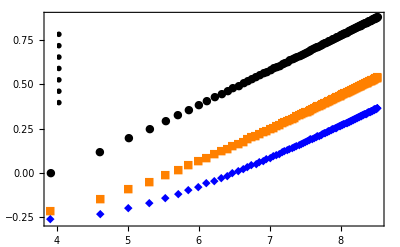

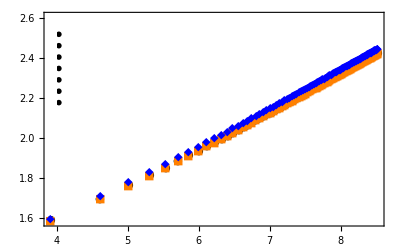

```mathematica
fig18=ListLogLogPlot[{f0,f1,f2,f3,f4,f5,f20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"∟"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
fig19=ListLogLogPlot[{g0,g1,g2,g3,g4,g5,g20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"||"]},LabelStyle->{Medium},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0},PlotMarkers->{Automatic,Tiny}]
```

### γ = 800

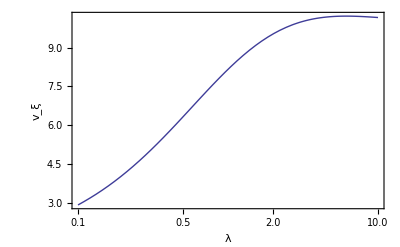

```mathematica
γ=10;
L=1;
fig20=LogLinearPlot[{π^(1/4)*((Evaluate[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*(Evaluate[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)^(1/2))/(300*√(8*γ))-π^(1/4)*((Evaluate[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*(Evaluate[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)^(1/2))/(300*√(8*γ))},{λ,0.1,10},RotateLabel->False,FrameLabel->{λ,Subscript[v,ξ]},PlotRange->All,Frame->True,Axes->False]
ClearAll[L,γ]
```

```mathematica
ClearAll[f0,f1,f2,f3,f4,f5,f20,g0,g1,g2,g3,g4,g5,g20]
γ=800;
L=0;
f0=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g0=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=1;
f1=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g1=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0,10,0.1}];
ClearAll[L]
L=2;
f2=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g2=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L];
L=3;
f3=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g3=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=4;
f4=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0,10,0.1}];
g4=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L];
L=5;
f5=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g5=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=20;
f20=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g20=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L,γ]
```

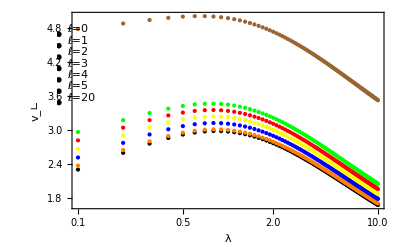

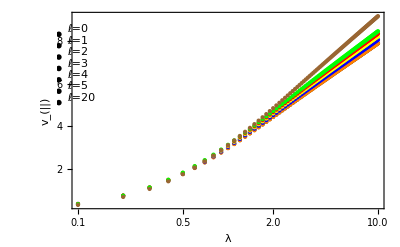

```mathematica
fig21=ListLogLinearPlot[{f0,f1,f2,f3,f4,f5,f20},RotateLabel->False,FrameLabel->{λ,Subscript[v,"∟"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0}]
fig22=ListLogLinearPlot[{g0,g1,g2,g3,g4,g5,g20},RotateLabel->False,FrameLabel->{λ,Subscript[v,"||"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0}]
```

### γ = 5

```mathematica
ClearAll[f0,f1,f2,f3,f4,f5,f20,g0,g1,g2,g3,g4,g5,g20]
γ=5;
L=0;
f0=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g0=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=1;
f1=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g1=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0,10,0.1}];
ClearAll[L]
L=2;
f2=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g2=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L];
L=3;
f3=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g3=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=4;
f4=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0,10,0.1}];
g4=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L];
L=5;
f5=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g5=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L]
L=20;
f20=Table[{λ,(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)*√(L+1)/300-(First[R[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)*√(L+1)/300},{λ,0.1,10,0.1}];
g20=Table[{λ,(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->1000)/300-(First[Z[t]/.NDSolve[{exp1,exp2,R[0]==Evaluate[r0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],Z[0]==Evaluate[z0/.FindRoot[{eqs1,eqs2},{r0,0.01},{z0,0.01}]],R'[0]==0,Z'[0]==0},{R[t],Z[t]},{t,0,1000}]]/.t->700)/300},{λ,0.1,10,0.1}];
ClearAll[L,γ]
```

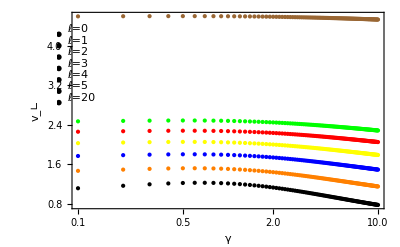

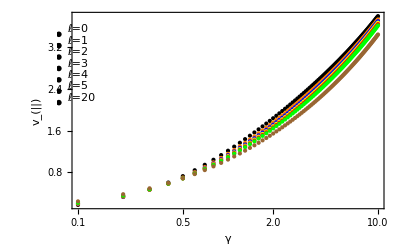

```mathematica
fig23=ListLogLinearPlot[{f0,f1,f2,f3,f4,f5,f20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"∟"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0}]
fig24=ListLogLinearPlot[{g0,g1,g2,g3,g4,g5,g20},RotateLabel->False,FrameLabel->{γ,Subscript[v,"||"]},PlotRange->All,Frame->True,Axes->False,PlotStyle->{Black,Orange,Blue,Yellow,Red,Green,Brown},PlotLegend->{"ℓ=0","ℓ=1","ℓ=2","ℓ=3","ℓ=4","ℓ=5","ℓ=20"},LegendTextSpace->5,LegendSize->{0.3,0.5},LegendPosition->{-0.74,0.05},LegendShadow->{0,0}]
```

## Exporting

```mathematica
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig1.eps",fig1]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig2.eps",fig2]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig3.eps",fig3]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig4.eps",fig4]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig5.eps",fig5]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig6.eps",fig6]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig7.eps",fig7]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig8.eps",fig8]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig9.eps",fig9]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig10.eps",fig10]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig11.eps",fig11]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12.eps",fig12]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13.eps",fig13]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig20.eps",fig20]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig21.eps",fig21]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig22.eps",fig22]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig23.eps",fig23]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig24.eps",fig24]
```

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig1.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig2.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig3.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig4.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig5.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig6.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig7.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig8.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig9.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig10.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig11.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig20.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig21.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig22.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig23.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig24.eps

```mathematica
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig14.eps",fig14]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig15.eps",fig15]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig16.eps",fig16]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig17.eps",fig17]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig18.eps",fig18]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig19.eps",fig19]
```

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig14.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig15.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig16.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig17.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig18.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig19.eps

```mathematica
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13b.eps",fig13b]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13.eps",fig13]
```

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13b.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig13.eps

```mathematica
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12.eps",fig12]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12a.eps",fig12a]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12b.eps",fig12b]
Export["Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12c.eps",fig12c]
```

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12a.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12b.eps

Dropbox/Trabalhos/free expansion vortices/1-FreeExpansionMultiplyCV-fig12c.eps